# PL/0 Compiler

References

- Introduction to the Theory of Computation, Michael Sipser	.
- Gate lectures by Ravindrababu Ravula: Compiler design.

Overview

This parser uses a finite automaton to recognize regular expressions which are also used by the lexical analyzer (lexer) to define the tokens to recognize. The input specified by the user is converted into a list of tokens and then is passed to the parser which builds a parse tree based on a given grammar. The grammar also has associated actions that are instructions that describe how to synthesize the tree into an intermediate code (IC) representation.

## Initialization

Finite state machine

### Deterministic finite automaton (DFA)

In the theory of computation, a branch of theoretical computer science, a deterministic finite automaton (DFA)—also known as deterministic finite acceptor (DFA), deterministic finite state machine (DFSM), or deterministic finite state automaton (DFSA)—is a finite-state machine that accepts or rejects strings of symbols and only produces a unique computation (or run) of the automaton for each input string.

DFAs recognize exactly the set of regular languages, which are, among other things, useful for doing lexical analysis and pattern matching. DFAs can be built from nondeterministic finite automata (NFAs) using the powerset construction method. This is useful because usually NFA are slower to compute.

DFA[name, transitions, start, accept, stateExpr] create an DFA from a transition list.
DFATransitions[transitions, state]
DFAIterate[transitions, state, inputSymbol] get the next step in the computation of the DFA for a inputSymbol.
DFACompute[dfa, inputString] compute if input is recognized by dfa.
FiniteAutomataPlot[fa] return a plot of the finite automata represented by fa.
DFAExecutionPlot[dfa, inputString] return a dynamic execution plot of the computation performed by dfa.

```mathematica
Protect[ϵ]; (* ϵ will be used as a symbol to denote the empty string *)
Transition[parent_,child_,inputSymbol_]:=<|"Parent"->parent,"Node"->child,"InputSymbol"->inputSymbol|>;
EmptyTransition[parent_,child_]:=Transition[parent,child,ϵ];
FATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];
Concatenate[l_]:=Apply[Join,l];
```

```mathematica
NameTag[machine_Association,state_]:=Subscript[machine["Name"],ToString[state]];

Options[FiniteAutomataPlot]={"Legended"->True,"Labeled"->False};
FiniteAutomataPlot[fa_Association,OptionsPattern[]]:=Block[{graphData,startTag,acceptTags,legend,graph},
Switch[OptionValue["Labeled"],
True,
graphData = Cases[fa["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = fa["StartState"]->Red;
acceptTags = Map[If[# ≠ fa["StartState"],#->Green,#->Purple]&,fa["AcceptStates"]];
,
False,
graphData = Cases[fa["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>p->n];
startTag = fa["StartState"]->Red;
acceptTags = Map[If[# ≠ fa["StartState"],#->Green,#->Purple]&,fa["AcceptStates"]];
];

legend = PointLegend[{LightBlue,Red,Green,Purple},{"State","Start state","Accept state","Start/Accept state"},LegendMarkers->Graphics[Disk[]]];

graph = Graph[
graphData,
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
];

If[OptionValue["Legended"],
Return[Legended[graph,legend]],
Return[graph]
]
];
```

```mathematica
(* DFA object constructor *)
DFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,(* Descriptive name to keep in track the regular operations applied to it *)
"Type"->"DFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept,
"StateExpressions"->stateExpr (* Each state may have an associated expression *)
|>;

(* Return every deterministic transition leading to state *)
DFATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];

(* Get the next state *)
Options[DFAIterate]={"Trace"->False};
DFAIterate[transitions_,state_,inputSymbol_,OptionsPattern[]]:=Block[{next},
next = Cases[
DFATransitions[transitions,state],
KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]
];

(* A DFA must have only one available transition *)
If[Length[next]==1,
If[OptionValue["Trace"],
Return[First[next]]
,
Return[First[next]["Node"]];
]
,
(* TODO: Crear mecanismo de alerta *)
Return[$Failed];
]
];

(* Returns the trace of the computation and the result of whether the machine accepts the inputString *)
DFACompute[dfa_Association,inputString_]:=Block[{computation,result},
computation = FoldList[
DFAIterate[dfa["Transitions"],#1["Node"],#2,"Trace"->True]&,
<|"Node"->dfa["StartState"]|>,
inputString
];
result = MemberQ[dfa["AcceptStates"],Last[computation]["Node"]];
Return[{computation,result}]
];
```

Plotting functions

```mathematica
Options[DFAExecutionPlot] = {"SimpleNodes"->False};
DFAExecutionPlot[dfa_Association,inputString_,OptionsPattern[]]:=DynamicModule[{trace,executionSteps,ruleIndexes,graphData,startTag,acceptTags},
trace = DFACompute[dfa,inputString];
executionSteps = Drop[First[trace],1];
ruleIndexes = Map[Position[dfa["Transitions"],#]&,executionSteps];

If[OptionValue["SimpleNodes"],
graphData = Cases[dfa["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = dfa["StartState"]->Red;
acceptTags = Map[#->Green&,dfa["AcceptStates"]];
,
graphData = Cases[dfa["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[NameTag[dfa,p]->NameTag[dfa,n],i]];
startTag = NameTag[dfa,dfa["StartState"]]->Red;
acceptTags = Map[NameTag[dfa,#]->Green&,dfa["AcceptStates"]];
];

Manipulate[
Column[
{
Row[{"Input string: ",Grid[{inputString},Frame->All,Background->{i->Green}]}],
Row[{"Result: ",If[Last[trace],"Accepted","Not accepted"]}],
Graph[
MapAt[Style[#,Red]&,graphData,ruleIndexes[[i]]],
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
]
}
]
,
{i,1,Length[ruleIndexes],1}
]
];
```

#### Examples

DFA declaration, where L(m_1) = {ω | ω contains at least one 1 and an even number of 0s follow the last 1}.

```mathematica
m1 = DFA[
"q",
{
Transition[1,1,{0}],
Transition[1,2,{1}],
Transition[2,2,{1}],
Transition[2,3,{0}],
Transition[3,2,{0,1}]
},
1,
{2}
]
```

<|Name→q,Type→DFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>},StartState→1,AcceptStates→{2},StateExpressions→{}|>

Plot of m_1

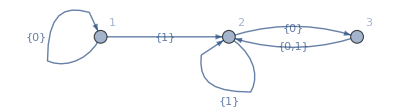

```mathematica
FiniteAutomataPlot[m1,"Labeled"->True]
```

Trace of the computation

```mathematica
DFACompute[m1,{1,0,1,0,0}]
```

{{<|Node→1|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>},True}

Plot of the execution with 10100 as input

```mathematica
DFAExecutionPlot[m1,{1,0,1,0,0}]
```

DFA declaration, where L(m_2) = {ω | ω ends in a 1}.

```mathematica
m2 = DFA[
"q",
{
Transition[1,1,{0}],
Transition[1,2,{1}],
Transition[2,2,{1}],
Transition[2,1,{0}]
},
1,
{2}
]
```

<|Name→q,Type→DFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>},StartState→1,AcceptStates→{2},StateExpressions→{}|>

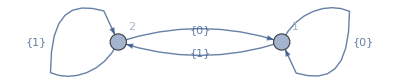

```mathematica
FiniteAutomataPlot[m2,"Labeled"->True]
```

```mathematica
DFACompute[m2,{1,0,1,0,0}]
```

{{<|Node→1|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→1,InputSymbol→{0}|>},False}

```mathematica
DFAExecutionPlot[m2,{1,1,1,0,1}]
```

### Non-deterministic Finite Automata (NFA)

In automata theory, a finite state machine is called a deterministic finite automaton (DFA), if

each of its transitions is uniquely determined by its source state and input symbol, and
reading an input symbol is required for each state transition.
A nondeterministic finite automaton (NFA), or nondeterministic finite state machine, does not need to obey these restrictions. In particular, every DFA is also an NFA. Sometimes the term NFA is used in a narrower sense, referring to a NFA that is not a DFA, but not in this article.

Using the subset construction algorithm, each NFA can be translated to an equivalent DFA, i.e. a DFA recognizing the same formal language. Like DFAs, NFAs only recognize regular languages.

NFA[name, transitions, start, accept, stateExpr] create an NFA from a transition list.
NFAIterate[transitions, state, inputSymbol] get the next step in the computation of the NFA for a inputSymbol.
NFACompute[nfa, inputString] compute if input is recognized by nfa.

NFASimplify[nfa] tries to simplify the structure of nfa by removing unnecesary nodes.
NFAUnion[nfa1, nfa2] perform the regular operation union.
NFAConcatention[nfa1, nfa2] perform the regular operation concatenation.
NFAStar[fa] perform the regular operation kleene star.
NFAToDFA[nfa] convert a NFA to a DFA by traversing every posible computation and transforming group of NFA states into a single DFA state.

NFAExecutionTreeComputeTrace[nfa, inputString] return the trace of the computation performed by nfa.
NFAExecutionTree[nfa, inputString] return the execution tree of the computation performed by nfa.
NFAExecutionPlot[nfa, inputString] return a dynamic execution plot of the computation performed by nfa.

```mathematica
NFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,
"Type"->"NFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept ,
"StateExpressions"->stateExpr
|>;

ContainsQ[list_List,form_]:=MemberQ[list,form];
ContainsQ[form1_,form2_]:=(form1===form2);

PureNondetStateQ[transitions_,state_]:=(DeleteDuplicates[FATransitions[transitions,state][[All,"InputSymbol"]]] === {ϵ});

(* Return the list of nodes accesible via empty transitions *)
NFANondetNodes[transitions_,state_Association]:=Cases[FATransitions[transitions,state["Node"]],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_Integer]:=Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_List]:=DeleteDuplicates[Flatten[Map[NFANondetNodes[transitions,#]&,state]]];
NFANondetNodesRecursive[transitions_,states_] := FixedPoint[DeleteDuplicates[Join[#,NFANondetNodes[transitions,#[[All,"Node"]]]]]&,states];

Options[NFAIterate]={"Trace"->False};
NFAIterate[transitions_,state_?AtomQ,inputSymbol_,OptionsPattern[]]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
(* Get all the transitions corresponding to a DFA *)
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

(* Run through the empty transitions of the DFA nodes *)
forkTransitions = NFANondetNodes[transitions,deterministicNodes]; (* Get past the current deterministic nodes *)
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions]; (* Append every valid nondet transition *)

(* The next nodes will be a union between the deterministic transitions and the nodes reachable from nondet transitions *)
next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,
If[OptionValue["Trace"],
Return[next],
Return[next[[All,"Node"]]]
]
,
Return[{}]
];
];
NFAIterate[transitions_,state_List,inputSymbol_,opt:OptionsPattern[]]:=DeleteDuplicates[Flatten[Map[NFAIterate[transitions,#,inputSymbol,opt]&,state]]];

NFACompute[nfa_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[
nfa["Transitions"],
{<|"Node"->nfa["StartState"]|>}
];
computation = FoldList[
NFAIterate[nfa["Transitions"],#1[[All,"Node"]],#2,"Trace"->True]&,
start,
inputString
];
result = Apply[Or,Map[MemberQ[nfa["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];
```

```mathematica
TransitionApplyThreshold[transition_,threshold_]:=MapAt[#+threshold&,transition,{{Key["Parent"]},{Key["Node"]}}];
MachineApplyThreshold[fa_Association,threshold_]:=<|
"Name"->fa["Name"],
"Transitions"->Map[TransitionApplyThreshold[#,threshold]&,fa["Transitions"]],
"StartState"->fa["StartState"]+threshold,
"AcceptStates"->fa["AcceptStates"]+threshold,
"StateExpressions"->If[Length[fa["StateExpressions"]]≠ 0,MapAt[#+threshold&,fa["StateExpressions"],{All,1}],{}]
|>;
```

```mathematica
GetDirectSuccesors[fa_,state_]:=Select[
Nest[NFANondetNodes[fa["Transitions"],#]&,{state},2],
(!ContainsQ[fa["AcceptStates"],#["Parent"]] &&PureNondetStateQ[fa["Transitions"],#["Parent"]] && Length[FAParents[fa["Transitions"],#["Parent"]]]==1)
&
];

ReplaceKey[assoc_,key_,replaceTo_]:=MapAt[replaceTo&,assoc,Key[key]];

DeleteIntermediateTransition[transitions_,startState_,endState_]:=Block[{deleteState,replacement,newTransitions,cleanedUp},
deleteState = endState["Parent"];
replacement = ReplaceKey[endState,"Parent",startState["Node"]];
cleanedUp = DeleteCases[transitions,KeyValuePattern["Parent"->deleteState]];
cleanedUp = DeleteCases[cleanedUp,KeyValuePattern["Node"->deleteState]];

newTransitions = Append[cleanedUp,replacement];
Return[newTransitions];
];

SimplifyStateIteration[nfa_,state_]:=Block[{newMachine,newTransitions},
newMachine = nfa;
newTransitions = Fold[
DeleteIntermediateTransition[#1,<|"Node"->state|>,#2]&,
nfa["Transitions"],
GetDirectSuccesors[nfa,state]
];
newMachine["Transitions"] = newTransitions;
Return[newMachine];
];
SimplifyState[nfa_,state_]:=FixedPoint[SimplifyStateIteration[#,state]&,nfa];

NFASimplify[nfa_]:=Block[{simplified,oldStates,newStates,stateRelabelRule = {}},
simplified = Fold[SimplifyState,nfa,GetStates[nfa["Transitions"]]];

oldStates = GetStates[simplified["Transitions"]];
newStates = Range[0,Length[oldStates]-1];
stateRelabelRule = Thread[oldStates->newStates];

simplified["Transitions"] = DeleteDuplicates[MapAt[Replace[#,stateRelabelRule]&,simplified["Transitions"],{{All,Key["Parent"]},{All,Key["Node"]}}]];
simplified["StartState"] = Replace[simplified["StartState"],stateRelabelRule];
simplified["AcceptStates"] = ReplaceAll[simplified["AcceptStates"],stateRelabelRule];
If[Length[simplified["StateExpressions"]]≠ 0,
simplified["StateExpressions"] = MapAt[Replace[#,stateRelabelRule]&,simplified["StateExpressions"],{All,1}];
];
Return[simplified];
];
```

```mathematica
NFAUnion[nfa1_Association,nfa2_Association]:=Block[{minIndex,newIndexThreshold,newM1,newM2,newAccept,newTransitions,newMachine,newStateExpressions},
minIndex = Min[nfa1["Transitions"][[All,"Parent"]]];
newIndexThreshold = Max[nfa1["Transitions"][[All,"Node"]]]+1;
newM1 = MachineApplyThreshold[nfa1,1];
newM2 = MachineApplyThreshold[nfa2,newIndexThreshold+1];
newAccept = Sort[Join[newM1["AcceptStates"],newM2["AcceptStates"]]];
newTransitions = {EmptyTransition[minIndex,newM1["StartState"]], EmptyTransition[minIndex,newM2["StartState"]]};
newStateExpressions = SortBy[Join[newM1["StateExpressions"],newM2["StateExpressions"]],First];

newMachine = <|
"Name"->StringJoin[nfa1["Name"],"∪",nfa2["Name"]],
"Type"->"NFA",
"Transitions"->Join[newM1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAUnion[nfas__/;Length[List[nfas]]>2]:=Fold[NFAUnion,First[List[nfas]],Rest[List[nfas]]];
```

```mathematica
NFAConcatention[nfa1_Association,nfa2_Association]:=Block[{newIndexThreshold,newM2,newTransitions,newMachine,newStateExpressions},
newIndexThreshold = Max[nfa1["Transitions"][[All,"Node"]]]+1;
newM2 = MachineApplyThreshold[nfa2,newIndexThreshold];

newTransitions = Map[EmptyTransition[#,newM2["StartState"]]&,nfa1["AcceptStates"]];

newStateExpressions = Join[nfa1["StateExpressions"],newM2["StateExpressions"]];
newStateExpressions = If[Length[newStateExpressions]≠ 0,SortBy[Join[nfa1["StateExpressions"],newM2["StateExpressions"]],First],{}];

newMachine = <|
"Name"->StringJoin[nfa1["Name"],nfa2["Name"]],
"Type"->"NFA",
"Transitions"->Join[nfa1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->nfa1["StartState"],
"AcceptStates"->newM2["AcceptStates"],
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAConcatention[fas__/;Length[List[fas]]>2]:=Fold[NFAConcatention,First[List[fas]],Rest[List[fas]]];
```

```mathematica
NFAStar[nfa_Association]:=Block[{minIndex,newM,newTransitions,newAccept,newFA},
minIndex = Min[nfa["Transitions"][[All,"Parent"]]];
newM = MachineApplyThreshold[nfa,1];
newTransitions = Join[{EmptyTransition[minIndex,newM["StartState"]]},Map[EmptyTransition[#,newM["StartState"]]&,newM["AcceptStates"]]];
newAccept = Append[newM["AcceptStates"],minIndex];

newFA = <|
"Name"->StringJoin["(",nfa["Name"],")^*"],
"Type"->"NFA",
"Transitions"->Join[newM["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newM["StateExpressions"]
|>;
Return[newFA];
];
```

```mathematica
(* Check if there is at least one of the accepted states in searchState *)
ContainsStateQ[stateList_,searchState_?AtomQ]:=MemberQ[stateList,searchState];
ContainsStateQ[stateList_,searchState_List]:=Apply[Or,Map[MemberQ[stateList,#]&,searchState]];

(* Get parents of the current state *)
FAParents[transitions_,state_]:=DeleteDuplicates[Cases[transitions,KeyValuePattern[{"Node"->state}]][[All,"Parent"]]];

(* Check if the state is inaccesible *)
JunkStateQ[transitions_,start_,state_]:=Block[{stateParents,nonSelfTransitions},
If[ContainsStateQ[start,state],Return[False]];
stateParents = FAParents[transitions,state];
nonSelfTransitions = Complement[stateParents,{state}];
If[Length[nonSelfTransitions]==0,
Return[True],
Return[False]
]
];

SafeSort[l_List]:=Sort[l];
SafeSort[l_?AtomQ]:=l;

(* Infer the alphabet from the transition list *)
GetAlphabet[transitions_]:=DeleteCases[DeleteDuplicates[Flatten[transitions[[All,"InputSymbol"]]]],ϵ];

(* Infer the states from the transition list *)
GetStates[transitions_]:=Sort[DeleteDuplicates[Flatten[Cases[transitions,KeyValuePattern[{"Parent"->p_,"Node"->n_}]:>{p,n}]]]];

(* Get the states reachable from the current states list *)
Explore[transitions_,states_]:=Map[
Transition[
SafeSort[states],
SafeSort[DeleteDuplicates[NFAIterate[transitions,states,#,"Trace"->False]]],
{#}]&,
GetAlphabet[transitions]
];

(* Explore one step down each branch of the computation and append it to the explored branches list *)
StepDown[transitions_,branches_]:=DeleteDuplicates[
Flatten[
Join[
branches,
Map[
Explore[
transitions,
#["Node"]
]&,
branches
]
],
1]
];

NewStateNode[node_,newStateRules_]:=
<|
"Parent"->Replace[node["Parent"],newStateRules],
"Node"->Replace[node["Node"],newStateRules],
"InputSymbol"->node["InputSymbol"]
|>;

NFAToDFA[nfa_Association]:=Block[{protoDFA,start,protoDFAStates,newStateRules,newStates,containsAccept,newFA,newAccept,newStart,newTransitions,newTransitionsCleanedUp,protoDFAExpressionNodes,newStateExpressionsNodes},
If[nfa["Type"] =!= "NFA",Return[$Failed]];

(* Explore all paths until there is no unexplored transition *)
start = 
FixedPoint[
DeleteDuplicates[
Join[
#,
NFANondetNodes[nfa["Transitions"],#[[All,"Node"]]]]
]&,
{<|"Node"->nfa["StartState"]|>}
];

(* Make a DFA by exploring all possible paths in the NFA *)
protoDFA = FixedPoint[StepDown[nfa["Transitions"],#]&,{<|"Node"->start[[All,"Node"]]|>}];
protoDFAStates = DeleteDuplicates[Join[Drop[protoDFA,1][[All,"Parent"]],Drop[protoDFA,1][[All,"Node"]]]];

(* Match old NFA parameters to the new DFA *)
newStateRules = Thread[protoDFAStates->Range[Length[protoDFAStates]]];
newStates =newStateRules[[All,2]];
containsAccept = Position[protoDFAStates,s_/;ContainsStateQ[s,nfa["AcceptStates"]]];
newAccept = Extract[newStates,containsAccept];
newStart = Replace[First[protoDFAStates],newStateRules];
newTransitions = Map[NewStateNode[#,newStateRules]&,Drop[protoDFA,1]];
newTransitionsCleanedUp = DeleteDuplicates[DeleteCases[newTransitions,t_/; JunkStateQ[newTransitions,newStart,t["Node"]]]];

protoDFAExpressionNodes = Concatenate[
Map[
Thread[Cases[protoDFAStates,s_/;ContainsStateQ[s,First[#]]]->Last[#]]&,
nfa["StateExpressions"]
]
];
If[Length[protoDFAExpressionNodes]≠0,
newStateExpressionsNodes = MapAt[Replace[#,newStateRules]&,protoDFAExpressionNodes,{All,1}]
,
newStateExpressionsNodes = {}
];

newFA = <|
"Name"->nfa["Name"],
"Type"->"DFA",
"Transitions"->newTransitionsCleanedUp,
"StartState"->newStart,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressionsNodes
|>;
Return[newFA];
];
```

Plotting functions

```mathematica
(* Pretty output for NFAExecutionTree *)
GenerationTransform[node_Association,generation_]:={
StringJoin["G: ",ToString[generation-1]," S: ",ToString[node["Parent"]]]->StringJoin["G: ",ToString[generation]," S: ",ToString[node["Node"]]]
,
ToString[node["InputSymbol"]]
};
GenerationTransform[nodes_List,generation_]:=Map[GenerationTransform[#,generation]&,nodes];

NFAReplaceParents[transitions_,newParent_]:=Map[MapAt[newParent&,#,Key["Parent"]]&,transitions];

NFAExecutionTreeIterate[transitions_,state_?AtomQ,inputSymbol_]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

forkTransitions = NFANondetNodes[transitions,deterministicNodes];
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions];
forkTransitions = NFAReplaceParents[forkTransitions,state]; (* This is the only difference from NFAIterate *)

next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,Return[next],Return[{}]];
];
NFAExecutionTreeIterate[transitions_,state_List,inputSymbol_]:=DeleteDuplicates[Flatten[Map[NFAExecutionTreeIterate[transitions,#,inputSymbol]&,state]]];

NFAExecutionTreeComputeTrace[nfa_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[nfa["Transitions"],{<|"Node"->nfa["StartState"]|>}]; (* This is the only difference from NFACompute *)
computation = FoldList[NFAExecutionTreeIterate[nfa["Transitions"],#1[[All,"Node"]],#2]&,start,inputString];
result = Apply[Or,Map[MemberQ[nfa["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];

(* Plot the execution tree showing the active states at every input *)
NFAExecutionTree[nfa_Association,inputString_]:=Block[{trace,root,traceTree},
trace = Drop[First[NFAExecutionTreeComputeTrace[nfa,inputString]],1];
root = First[GenerationTransform[First[trace],1]];
traceTree = Flatten[MapIndexed[GenerationTransform[#1,First[#2]]&,trace],1];

TreePlot[
DeleteDuplicates[traceTree],
Automatic,StringJoin["G: 0 S: ",ToString[nfa["StartState"]]],

VertexLabeling->True,
DirectedEdges->True
]
];

Options[NFAExecutionPlot] = {"SimpleNodes"->False};
NFAExecutionPlot[nfa_Association,inputString_,OptionsPattern[]]:=DynamicModule[{trace,executionSteps,ruleIndexes,graphData,startTag,acceptTags,currentStates,start,parentStates},
trace = NFACompute[nfa,inputString];
executionSteps = First[trace];
ruleIndexes = Map[Position[nfa["Transitions"],Apply[Alternatives,#]]&,executionSteps];
currentStates = Cases[nfa["Transitions"],KeyValuePattern[{"Node"->n_}]:>n];
parentStates = Cases[nfa["Transitions"],KeyValuePattern[{"Parent"->p_}]:>p];
start = DeleteDuplicates[Sort[Join[{<|"Node"->nfa["StartState"]|>},NFANondetNodes[nfa["Transitions"],nfa["StartState"]]]]];

If[OptionValue["SimpleNodes"],
graphData = Cases[nfa["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
acceptTags = Map[#->Green&,nfa["AcceptStates"]];
startTag = nfa["StartState"]->Red;
,
graphData = Cases[nfa["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[NameTag[nfa,p]->NameTag[nfa,n],i]];
acceptTags = Map[NameTag[nfa,#]->Green&,nfa["AcceptStates"]];
startTag = NameTag[nfa,nfa["StartState"]]->Red;
];

Manipulate[
Column[
{
Row[{"Input string: ",Grid[{inputString},Frame->All,Background->{(i-1)->Green}]}],
Row[{"Start states: ",Sort[start[[All,"Node"]]]}],
Row[{"Parent states: ",Sort[Extract[parentStates,ruleIndexes[[i]]]]}],
Row[{"Current states: ",Sort[Extract[currentStates,ruleIndexes[[i]]]]}],
Row[{"Accept states: ",nfa["AcceptStates"]}],
Row[{"Result: ",If[Last[trace],"Accepted","Not accepted"]}],
Graph[
MapAt[Style[#,Red]&,graphData,ruleIndexes[[i]]],
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
]
}
]
,
{i,1,Length[ruleIndexes],1}
]
];
```

#### Examples

NFA declaration, where L(n_1) = {ω | ω contains either 101 or 11 as a substring}.

```mathematica
n1 = NFA[
"q",
{
Transition[1,1,{0,1}],
Transition[1,2,{1}],
Transition[2,3,{0,ϵ}],
Transition[3,4,{1}],
Transition[4,4,{0,1}]
},
1,
{4}
]
```

<|Name→q,Type→NFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0,1}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0,ϵ}|>,<|Parent→3,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→4,InputSymbol→{0,1}|>},StartState→1,AcceptStates→{4},StateExpressions→{}|>

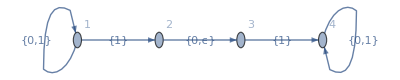

```mathematica
FiniteAutomataPlot[n1,"Labeled"->True]
```

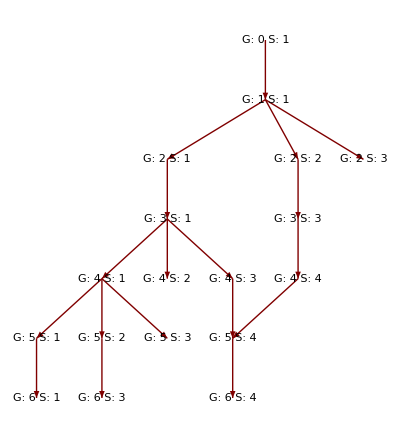

```mathematica
NFAExecutionTree[n1,{0,1,0,1,1,0}]
```

```mathematica
Column@First[NFACompute[n1,{0,1,0,1,1,0}]][[All,All,"Node"]]
```

{1}
{1}
{1,2,3}
{1,3}
{1,2,3,4}
{1,2,3,4,4}
{1,3,4}

```mathematica
NFAExecutionPlot[n1,{0,1,0,1,1,0}]
```

NFA declaration, where L(nfa) = 0 Σ^*1.

```mathematica
nfa = NFA[
"q",
{
Transition[0,1,{0}],
EmptyTransition[1,2],
EmptyTransition[1,3],
Transition[2,4,{1}],
EmptyTransition[4,1],
Transition[3,5,{0}],
EmptyTransition[5,1],
EmptyTransition[4,6],
EmptyTransition[5,6],
Transition[6,7,{1}]
},
0,
{7}
]
```

<|Name→q,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→3,Node→5,InputSymbol→{0}|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→6,Node→7,InputSymbol→{1}|>},StartState→0,AcceptStates→{7},StateExpressions→{}|>

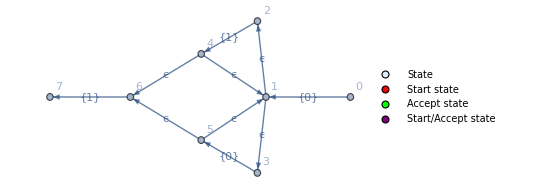

```mathematica
FiniteAutomataPlot[nfa,"Labeled"->True]
```

```mathematica
NFAExecutionPlot[nfa,{0,0,1,1,1}]
```

Union operation

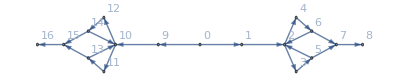

```mathematica
FiniteAutomataPlot@NFAUnion[nfa,nfa]
```

#### Applications

This automata recongnizes a

```mathematica
aNFA = NFA["a",{Transition[0,1,{"a"}]},0,{1}]
```

<|Name→a,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{a}|>},StartState→0,AcceptStates→{1},StateExpressions→{}|>

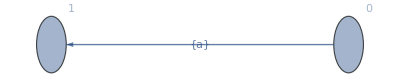

```mathematica
FiniteAutomataPlot[aNFA,"Labeled"->True]
```

and this one recognizes b

```mathematica
bNFA = NFA["b",{Transition[0,1,{"b"}]},0,{1}]
```

<|Name→b,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{b}|>},StartState→0,AcceptStates→{1},StateExpressions→{}|>

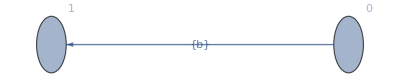

```mathematica
FiniteAutomataPlot[bNFA,"Labeled"->True]
```

The union of both, that is a ∪ b is represented by the NFA

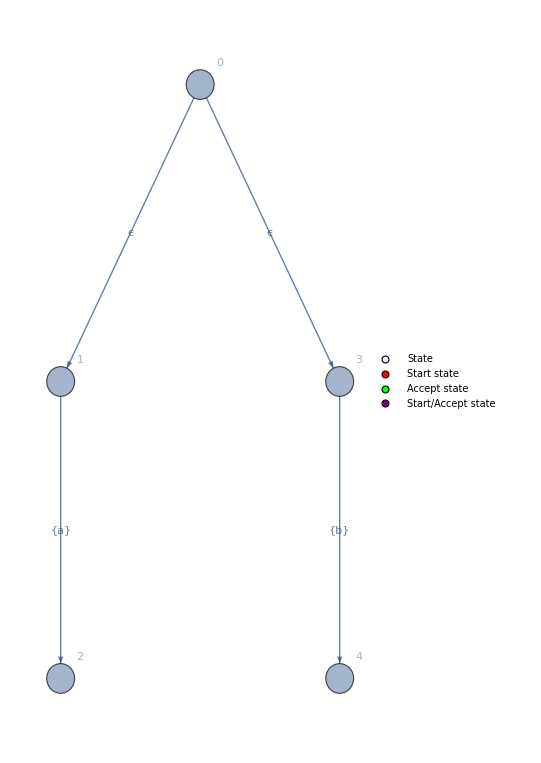

```mathematica
FiniteAutomataPlot[NFAUnion[aNFA,bNFA],"Labeled"->True]
```

Using various operations we can recognize (a ∪ (b))^*aba

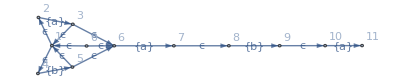

```mathematica
FiniteAutomataPlot[NFAConcatention[NFAStar[NFAUnion[aNFA,bNFA]],aNFA,bNFA,aNFA],"Labeled"->True]
```

```mathematica
example = NFAConcatention[NFAStar[NFAUnion[aNFA,bNFA]],aNFA,bNFA,aNFA]
```

<|Name→(a∪b)^*aba,Type→NFA,Transitions→{<|Parent→2,Node→3,InputSymbol→{a}|>,<|Parent→4,Node→5,InputSymbol→{b}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→4,InputSymbol→ϵ|>,<|Parent→0,Node→1,InputSymbol→ϵ|>,<|Parent→3,Node→1,InputSymbol→ϵ|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→6,Node→7,InputSymbol→{a}|>,<|Parent→3,Node→6,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→0,Node→6,InputSymbol→ϵ|>,<|Parent→8,Node→9,InputSymbol→{b}|>,<|Parent→7,Node→8,InputSymbol→ϵ|>,<|Parent→10,Node→11,InputSymbol→{a}|>,<|Parent→9,Node→10,InputSymbol→ϵ|>},StartState→0,AcceptStates→{11},StateExpressions→{}|>

```mathematica
NFAExecutionPlot[example,{"a","b","b","a","b","a"}]
```

```mathematica
NFAExecutionPlot[example,{"a","b","b","a","b","b"}]
```

Regular expressions

A regular expression, regex or regexp  is a sequence of characters that define a search pattern. Usually this pattern is used by string searching algorithms for “find” or “find and replace” operations on strings, or for input validation. It is a technique that developed in theoretical computer science and formal language theory.

This regex implementation is just a front-end to the Finite Automata operations.

Regex[c] creates a recognizer for the character c.
Regex[str, tokenRecognize]  creates a recognizer for the string str which classifies it as the token tokenRecognize.
RegexUnion[args] Perform the regular operation union. Can be applied to an arbitrary number of finite automate type arguments args.
RegexConcatenation[args] Perform the regular operation concatenation. Can be applied to an arbitrary number of finite automate type arguments args.
RegexStar[fa] perform the regular operation kleene star to a finite automata fa.
RegexStar[str] perform the regular operation kleene star to a string str.
RegexDagger[fa] perform the regular operation dagger to a finite automata fa.
RegexDagger[str]perform the regular operation dagger to a string str.

RegexAlphabet[alphabet] creates a recognizer for a string containing the alphabet.
RegexAlphabetLowercase[] lowercase alphabet wrapper.
RegexAlphabetUppercase[] uppercase alphabet wrapper.
RegexAlphabet[]  A...Za...z recognizer.
RegexDigits[] 0...9 recognizer.
RegexASCIIChars[] recognizes every char in the ASCII standard.

RegexCompute[fa, input] compute if input is recognized by fa, and if applicable, return the recognized token.

```mathematica
RegexUnion[args__]:=NFAUnion[args];
RegexConcatenation[args__]:=NFAConcatention[args];
RegexStar[fa_Association]:=NFAStar[fa];
RegexStar[str_String]:=NFAStar[Regex[str]];
RegexDagger[fa_Association]:=NFAConcatention[fa,NFAStar[fa]];
RegexDagger[str_String]:=NFAConcatention[Regex[str],NFAStar[Regex[str]]];
```

```mathematica
Regex[c_String/;StringLength[c]==1]:=NFA[c,{Transition[0,1,{c}]},0,{1}];
Regex[c_String/;StringLength[c]==1,stateExpr_]:=NFA[c,{Transition[0,1,{c}]},0,{1},{1->stateExpr}];
Regex[str_String/;StringLength[str]>1,tokenRecognize_:""]:=Block[{m},
m =Apply[NFAConcatention,Map[Regex,Characters[str]]];
If[tokenRecognize≠ "",
m["StateExpressions"] =Thread[m["AcceptStates"]->tokenRecognize];
];

Return[m];
];
Regex[r_Association,tokenRecognize_]:=Block[{m = r},
m["StateExpressions"] = Thread[m["AcceptStates"]->tokenRecognize];
Return[m];
];
```

```mathematica
RegexAlphabet[alphabet_]:=Block[{input,name,transitions,acceptStates,newFA},
input = Characters[alphabet];
newFA = <|
"Name"->StringJoin[Riffle[input,"∪"]],
"Type"->"NFA",
"Transitions"->Map[Transition[0,#,{input[[#]]}]&,Range[Length[input]]],
"StartState"->0,
"AcceptStates"->Range[Length[input]],
"StateExpressions"->{}
|>;
Return[newFA];
];

RegexAlphabetLowercase[]:=RegexAlphabet[StringJoin@Alphabet[]];
RegexAlphabetUppercase[]:=RegexAlphabet[StringJoin@ToUpperCase[Alphabet[]]];
RegexAlphabet[]:=RegexAlphabet[StringJoin@Join[Alphabet[],ToUpperCase[Alphabet[]]]];
RegexDigits[]:=RegexAlphabet[StringJoin@Map[ToString,Range[0,9]]];

asciiChars = {"\t","\n","\f","\r"," ","!","#","$","%","&","'","(",")","*","+",",","-",".","/","0","1","2","3","4","5","6","7","8","9",":",";","<","=",">","?","@","A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z","[","\\","]","^","_","`","a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z","{","|","}","~",".7f"};

RegexASCIIChars[]:=RegexAlphabet[StringJoin@asciiChars];
```

```mathematica
RegexCompute[fa_,input_]:=Block[{trace,result,recognizedTokens},
If[fa["Type"]== "NFA",
{trace,result} = NFACompute[fa,Characters[input]];
recognizedTokens = 
Cases[
Last[trace][[All,"Node"]],
(node_ /; ContainsQ[fa["StateExpressions"][[All,1]],node]):> Replace[node,fa["StateExpressions"]]
];

,
{trace,result} =DFACompute[fa,Characters[input]];
recognizedTokens = 
Cases[
{Last[trace]["Node"]},
(node_ /; ContainsQ[fa["StateExpressions"][[All,1]],node]):> Replace[node,fa["StateExpressions"]]
];
];

Return[{trace,result,recognizedTokens}];
];
```

Lexer

In computer science, lexical analysis, lexing or tokenization is the process of converting a sequence of characters (such as in a computer program or web page) into a sequence of tokens (strings with an assigned and thus identified meaning). A program that performs lexical analysis may be termed a lexer, tokenizer, or scanner, though scanner is also a term for the first stage of a lexer.

Token[symbol, name] is a token constructor.
CreateTokens[list] creates a token list from a list that contains {symbol, name} pairs.
CreateTokenRecognizer[tokenList] creates a recognizer (implemented as  a regular expression and using a finite automata as a backend) of every token in tokenList. 

GetToken[input, symbolTokens, keywordTokens] for a input string tries to match a symbol token or a keyword token. If no match is found it returns $Failed. Keyword tokens have precedence over symbol tokens.
GetNextToken[program, symbolTokens, keywordTokens] for a input string program, tries to match the biggest token from the left of the string. 
Tokenize[program, symbolTokens, keywordTokens] transform the input string program into a list of tokens by using the recognizers symbolTokens and keywordTokens.
Lint[program, symbolTokens, keywordTokens, colorRules] applies styling transfomations for each token.

```mathematica
(* 
   There are various types of tokens. Symbol tokens can be any simple expression like
  {"/", "Slash"},
   {"+", "Plus"},
   {"-", "Minus"},
   ...
  That cannot be confused with an identifier. It is necessary to make this distintion since keyword tokens like
  {"const", "Const"},
   {"var", "Var"},
   {"procedure", "Procedure"},
   {"call", "Call"},
   ...
  have the same form of identifiers, so the lexer has to give precedence to the keyword token. 
 *)
Token[symbol_String,name_String]:=<|"Symbol"->symbol,"Name"->name|>;
CreateTokens[list_]:=Map[Token[#[[1]],#[[2]]]&,list];
CreateTokenRecognizer[tokenList_]:=NFAToDFA[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenList]]];
```

```mathematica
GetToken[input_,symbolTokens_,keywordTokens_]:=Block[{symbolAccept,symbolResult,keywordAccept,keywordResult},
{symbolAccept,symbolResult} = Rest[RegexCompute[symbolTokens,input]];
{keywordAccept,keywordResult} = Quiet[Rest[RegexCompute[keywordTokens,input]]];
If[keywordAccept,Return[First[keywordResult]]]; (* Keywords have precedence over symbols *)
If[symbolAccept,Return[First[symbolResult]]];
Return[$Failed];
];

SafeStringTake[string_,n_]:=StringTake[string,Min[n,StringLength[string]]];
SafeStringTake[string_,{m_,n_}]:=StringTake[string,{m,Min[n,StringLength[string]]}];

GetNextToken::badInput = "There are input symbols that cannot be matched with any token.";
GetNextToken[program_,symbolTokens_,keywordTokens_]:=Block[{tokenizerResult,nextToken},
(* Try to get the first biggest token from the input *)
tokenizerResult = NestWhileList[
{
First[#]+1,
GetToken[SafeStringTake[program,First[#]+1],symbolTokens,keywordTokens]
}&,
{
0,
None
},
((Last[#]=!= $Failed)&&(First[#]≤StringLength[program]))&
];

(* If no tokens were matched, abort the compilation *)
If[tokenizerResult == {{0,None},{1,$Failed}},
Message[GetNextToken::badInput];
Abort[]
];

(* Select the last before GetToken failed *)
nextToken = If[Length[tokenizerResult]>2,tokenizerResult[[-2]],Last[tokenizerResult]];
Return[nextToken];
];

Options[Tokenize] = {"IncludeBlank"->False};
Tokenize[program_,symbolTokens_,keywordTokens_,OptionsPattern[]]:=Block[
{
length,type,
cursor = 0,
tokenList = {},
omitTokens ,
formattedTokens
},

If[OptionValue["IncludeBlank"],
omitTokens = {},
omitTokens = {"Whitespace","LineBreak"}
];

(* Iterate over all the input getting the tokens one by one *)
While[cursor<StringLength[program],
{length,type} = GetNextToken[StringDrop[program,cursor],symbolTokens,keywordTokens];
If[!MemberQ[omitTokens,type],AppendTo[tokenList,<|"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>]];
cursor+=length;
];

(* Tokens without value only carry type information *)
formattedTokens = Map[
If[#["Type"] =!=#["Value"],
<|
"Type"->#["Type"],
"Value"->#["Value"]
|>,
<|
"Type"->#["Type"]
|>
]
&,
tokenList
];

Return[formattedTokens];
];

Lint[program_,symbolTokens_,keywordTokens_,colorRules_]:=Block[{tokens,highlighted,linted},
tokens = Tokenize[program,symbolTokens,keywordTokens,"IncludeBlank"->True];
highlighted = Map[Style[#["Value"],#["Type"]/.colorRules]&,tokens];
Return[Row[highlighted]];
];
```

### Example

A lexer for simple arithmetic parser

```mathematica
arithmeticTokenSymbols = CreateTokens[
{
{" ","Whitespace"},
{"*", "*"},
{"+", "+"},
{"(", "("},
{")", ")"}
}
];
arithmeticTokenSymbolsNFA = NFASimplify[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,arithmeticTokenSymbols]]];
arithmeticTokenSymbolsDFA = NFAToDFA[arithmeticTokenSymbolsNFA];
idLiteral = Regex[NFAToDFA[RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]]],"id"];
```

```mathematica
tokens = Tokenize["5+6*(7+9)",arithmeticTokenSymbolsDFA,idLiteral]
```

{<|Type→id,Value→5|>,<|Type→+|>,<|Type→id,Value→6|>,<|Type→*|>,<|Type→(|>,<|Type→id,Value→7|>,<|Type→+|>,<|Type→id,Value→9|>,<|Type→)|>}

Parser

Parsing, syntax analysis, or syntactic analysis is the process of analysing a string of symbols, either in natural language, computer languages or data structures, conforming to the rules of a formal grammar. A parser is a software component that takes input data (frequently text) and builds a data structure – often some kind of parse tree, abstract syntax tree or other hierarchical structure, giving a structural representation of the input while checking for correct syntax.

In this project a recursive descent parser is used.  A recursive descent parser is a kind of top-down parser built from a set of mutually recursive procedures (or a non-recursive equivalent) where each such procedure implements one of the nonterminals of the grammar. Thus the structure of the resulting program closely mirrors that of the grammar it recognizes.

### Grammar beautification

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["To"],{NonTerm[arg_]:>Style[arg,Bold],Term[arg_]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[Map[GrammarPrettifyRule,grammar]];

GrammarGraph[grammar_]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle]
];
```

### Rule matching

MatchTerminalsWithRule[stateId, lastId, input, rule] try to match the input with a production rule from the grammar. stateId and lastId are labels to avoid ambiguity in the parse tree.
MatchTerminals[{state, stateId}, lastId, input, grammar] tries to match the input with every production rule in grammar. This is used for the parse process.

```mathematica
Protect[EmptyString,Term,NonTerm];

GetArgument[_[arg_]]:=arg;
Substitute[l1_,l2_]:=Join[l1,Drop[l2,Length[l1]]];

TermMatchQ[input_,{}]:=True;
TermMatchQ[input_,terms_]:=(Take[input,Length[terms]][[All,"Type"]] == Map[GetArgument,terms]);
GenerateTransitions[rule_,stateId_,lastId_]:=MapIndexed[{rule["From"],stateId}->{#1,lastId+First[#2]}&,rule["To"]];

MatchTerminalsWithRule[stateId_,lastId_,input_,rule_]:=Block[{terms,transition,rest,cuttedInput,currentState,lastIndex,matchTransitions},
currentState = rule["From"];
If[rule["To"]===EmptyString[],Return[{{{currentState,stateId}->{EmptyString[],lastId+1}},{},input,lastId+1}]];

(* 
   GenerateTransitions creates a list of every transition that can be obtained from a single rule. For example:
 GenerateTransition[<|"From"->a,"To"->{b,c,d}|>, 1, 4] will return
{{a,1}->{b,5},{a,1}->{c,6},{a,1}->{d,7}}
 *)
transition = GenerateTransitions[rule,stateId,lastId];
lastIndex = Last@Last@Last@transition;
terms = TakeWhile[rule["To"],Head[#]=!=NonTerm&]; (* Consume every symbol until it encounters a NonTerminal *)
rest = Drop[transition[[All,2]],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[TermMatchQ[input,terms], (* If consumed terms coincide with input *)
matchTransitions =MapIndexed[
If[KeyExistsQ[#1,"Value"],
{rule["From"],stateId}->{Term[#1["Type"]],lastId+First[#2],#1["Value"]},
{rule["From"],stateId}->{Term[#1["Type"]],lastId+First[#2]}
]&,
Take[input,Length[terms]]
];
transition = Substitute[matchTransitions,transition];
cuttedInput = Drop[input,Length[terms]];
Return[{transition,rest,cuttedInput,lastIndex}];
,
Return[$Failed];
];
];

MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

(* Try to match the input with every rule in the grammar *)
MatchTerminals[{state_,stateId_},lastId_,input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->state}]];
matched = Last[MapUntil[{#,MatchTerminalsWithRule[stateId,lastId,input,#]}&,possibleTransitions,Last[#]=!=$Failed&]];
Return[matched];
];
```

#### Example

Given a simple arithmetic grammar

```mathematica
arithmeticGrammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString[]|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString[]|>
};
GrammarPrettify[arithmeticGrammar]
```

NonTerm[E]→{i,E',V}
NonTerm[V]→{j,V}
NonTerm[V]→EmptyString[]
NonTerm[E']→{+,i,E'}
NonTerm[E']→EmptyString[]

and the input i+i

```mathematica
testInput = Map[<|"Type"->#|>&,{"i","+","i"}]
```

{<|Type→i|>,<|Type→+|>,<|Type→i|>}

If we try to match with the rule E’ -> + i E’ since i can’t match with + the function will return false.

```mathematica
MatchTerminalsWithRule[1,4,testInput,<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>]
```

$Failed

If we try to match with the rule E -> i E’ V it will list the full transition,

```mathematica
{transition,rest,cuttedInput,lastIndex} = MatchTerminalsWithRule[1,4,testInput,<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>];
```

```mathematica
transition
```

{{NonTerm[E],1}→{Term[i],5},{NonTerm[E],1}→{NonTerm[E'],6},{NonTerm[E],1}→{NonTerm[V],7}}

the unmatched symbols of the rule,

```mathematica
rest
```

{{NonTerm[E'],6},{NonTerm[V],7}}

the remaining input

```mathematica
cuttedInput
```

{<|Type→+|>,<|Type→i|>}

and the last index used by the counter.

```mathematica
lastIndex
```

7

We can try with all the rules in the grammar at once and choose the first  rule that matches.

```mathematica
MatchTerminals[{NonTerm["E"],1},4,testInput,arithmeticGrammar]
```

{<|From→NonTerm[E],To→{Term[i],NonTerm[E'],NonTerm[V]}|>,{{{NonTerm[E],1}→{Term[i],5},{NonTerm[E],1}→{NonTerm[E'],6},{NonTerm[E],1}→{NonTerm[V],7}},{{NonTerm[E'],6},{NonTerm[V],7}},{<|Type→+|>,<|Type→i|>},7}}

### Parser

VerifyGrammar[grammar] verifies the correctness of grammar.
VerifyInput[tokenList] verifies the correctness of an input to be parsed in the form of a tokenList.
Parse[input, grammar] parses input in the form of a token list and returns a parse tree and semantic actions associated with every NonTerminal of the parse tree.
ParseTree[input, grammar] returns a graphical representation of the parse tree generated by Parse.

```mathematica
Protect[$IncompleteGrammar];
VerifyGrammar[grammar_]:=Block[{grammarKeys},
grammarKeys = DeleteDuplicates[Map[Keys,grammar]];
If[grammarKeys=={{"From","To","Action"}}, Return[True]];
If[MemberQ[grammarKeys, {"From","To"}], Return[$IncompleteGrammar]];
Return[False];
];
VerifyInput[tokenList_]:=Block[{inputKeys},
(* Input must be a list of tokens with Type and Value entries. *)
inputKeys = DeleteDuplicates[Map[Keys,tokenList]];
If[inputKeys == {{"Type","Value"}}, 
Return[True],
Return[False]
];
];

Options[Parse]={"Trace"->False};
Parse::incompleteGrammar = "Actions in this grammar are not correctly specified";
Parse::badGrammar = "Incorrect grammar";
Parse::badInput = "Incorrect input";
Parse[input_,grammar_,OptionsPattern[]]:=Block[{grammarCheck,pGrammar,trace,symbolRules,rule,stack,transitions,next,inputBuffer,lastId,parseTree,parseSymbol,toStack},
(* Error check *)
grammarCheck = VerifyGrammar[grammar];
If[grammarCheck == False,
Message[Parse::badGrammar];
Abort[];
];
If[grammarCheck ===$IncompleteGrammar,Message[Parse::incompleteGrammar]];
If[VerifyInput[input] == False,
Message[Parse::badInput];
Abort[];
];

(* Initialization *)
pGrammar = MapAt[NonTerm,grammar,{All,Key["From"]}];
stack = {};
parseTree = {};
lastId = 1;
inputBuffer = input;
parseSymbol = {First[pGrammar]["From"],1};
symbolRules = {};
trace = {<|"ParseSymbol"->parseSymbol,"Stack"->stack,"LastID"->lastId,"InputBuffer"->inputBuffer|>};

(* Loop until there are no input symbols left and no symbol left to parse *)
While[{inputBuffer,parseSymbol} =!= {{},None},
If[Head[First[parseSymbol]] ===NonTerm,

(* Case where the parse symbol is a non terminal *)
{rule,{transitions,next,inputBuffer,lastId} } = MatchTerminals[parseSymbol,lastId,inputBuffer,pGrammar];
AppendTo[parseTree,transitions];
AppendTo[symbolRules,{parseSymbol,rule["Action"]}];
,
(* Case where the parse symbol is a terminal *)
If[GetArgument[First[parseSymbol]] == First[inputBuffer]["Type"],
inputBuffer =Drop[inputBuffer,1];
next = {};
];
];

If[Length[next]>0,
(* If there are symbols left to process, process the first and push the rest to the stack *)
{parseSymbol,toStack}={First[next],Reverse[Rest[next]]};
stack = Join[stack,toStack];
,
(* If there are no symbols left, pop one from the stack *)
If[Length[stack] > 0,
{parseSymbol,stack}={Last[stack],Drop[stack,-1]};
,
(* Flag to stop the loop when the stack is empty *)
parseSymbol = None;
];
];

AppendTo[trace,<|"ParseSymbol"->parseSymbol,"Stack"->stack,"LastID"->lastId,"InputBuffer"->inputBuffer|>]
];

parseTree = Flatten[parseTree,1];

If[OptionValue["Trace"],
Return[trace],

If[grammarCheck ===$IncompleteGrammar,
Return[{parseTree,{}}]
,
Return[{parseTree,symbolRules}]
]
];
];

ParseTree[input_,grammar_]:=Block[{parseTree,startProduction,styledParseTree,styleRules},
parseTree = First@Parse[input,grammar];
styleRules = {NonTerm[x_]:>Style["NonTerm("<>ToString[x]<>")",Blue],Term[x_]:>Style["Term("<>ToString[x]<>")",Red]};
styledParseTree = ReplaceAll[parseTree,styleRules];
startProduction = First[First[styledParseTree]];
TreePlot[styledParseTree,Automatic,startProduction,VertexLabeling->True,AspectRatio->1/4]
];
```

#### Example

We can build a parse tree from the arithmetic grammar. Notice that the head NonTerm can be omitted in the “From” key since every from symbol must be a NonTerminal by definition.

```mathematica
arithmeticGrammar = {
<|"From"->"E","To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->"V","To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->"V","To"->EmptyString[]|>,
<|"From"->"E'","To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->"E'","To"->EmptyString[]|>
};
```

```mathematica
GrammarPrettify[arithmeticGrammar]
```

E→{i,E',V}
V→{j,V}
V→EmptyString[]
E'→{+,i,E'}
E'→EmptyString[]

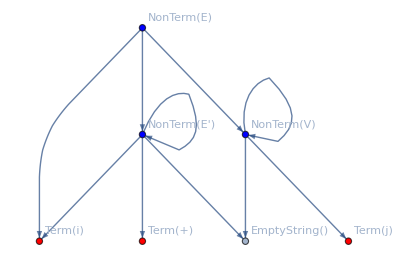

```mathematica
GrammarGraph[arithmeticGrammar]
```

```mathematica
testInput = Map[<|"Type"->#,"Value"->#|>&,{"i","+","i"}];
```

```mathematica
VerifyInput[testInput]
```

True

Since no actions are specified in this grammar, a warning is given about the grammar being incomplete.

```mathematica
Parse[testInput,arithmeticGrammar]
```

{{{NonTerm[E],1}→{Term[i],2,i},{NonTerm[E],1}→{NonTerm[E'],3},{NonTerm[E],1}→{NonTerm[V],4},{NonTerm[E'],3}→{Term[+],5,+},{NonTerm[E'],3}→{Term[i],6,i},{NonTerm[E'],3}→{NonTerm[E'],7},{NonTerm[E'],7}→{EmptyString[],8},{NonTerm[V],4}→{EmptyString[],9}},{}}

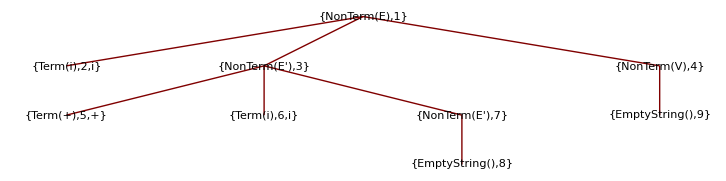

```mathematica
ParseTree[testInput,arithmeticGrammar]
```

## PL/0 Implementation

Lexer tokens definition

Here we define the tokens that will be recognized by the lexer.

```mathematica
tokenSymbols = CreateTokens[
{
{" ","Whitespace"},
{"\n", "LineBreak"},
{":", "IncompleteAssign"},
{":=", "Assign"},
{"*", "Times"},
{"/", "Slash"},
{"+", "Plus"},
{"-", "Minus"},
{"=", "Equal"},
{"#", "NotEqual"},
{"(", "LeftParenthesis"},
{")", "RightParenthesis"},
{";", "Semicolon"},
{",", "Comma"},
{".", "Dot"},
{">", "Greater"},
{">=", "GreaterOrEqual"},
{"<", "Lower"},
{"<=", "LowerOrEqual"}
}
];
tokenKeywords = CreateTokens[
{
{"const", "Const"},
{"var", "Var"},
{"procedure", "Procedure"},
{"call", "Call"},
{"print", "Print"},
{"begin", "Begin"},
{"end", "End"},
{"if", "If"},
{"then", "Then"},
{"while", "While"},
{"do", "Do"},
{"odd", "Odd"}
}
];

tokenSymbolsRecognizer = CreateTokenRecognizer[tokenSymbols];
keywordRecognizer = CreateTokenRecognizer[tokenKeywords];

identifierRegex =RegexConcatenation[RegexAlphabet[],RegexStar[RegexUnion[RegexAlphabet[],RegexDigits[]]]];
numberLiteralRegex = RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]];

identifierRecognizer = Regex[identifierRegex,"Identifier"];
numberLiteralRecognizer = Regex[numberLiteralRegex,"NumberLiteral"];
symbolRecognizer= RegexUnion[identifierRecognizer,numberLiteralRecognizer,tokenSymbolsRecognizer];
```

```mathematica
(* Used for linting *)
colorRules = {
"Var"->RGBColor[0.33, 0.6, 0.],
"Const"->RGBColor[0.33, 0.6, 0.],
"NumberLiteral"->RGBColor[0.76, 0.37, 0.],
"Procedure"->RGBColor[0., 0.32, 1.],
"Call"->RGBColor[0.55, 0., 0.8200000000000001],
"Print"->RGBColor[0.55, 0., 0.8200000000000001],
"Begin"->RGBColor[0.55, 0., 0.8200000000000001],
"End"->RGBColor[0.55, 0., 0.8200000000000001],
"If"->RGBColor[0.55, 0., 0.8200000000000001],
"Then"->RGBColor[0.55, 0., 0.8200000000000001],
"While"->RGBColor[0.55, 0., 0.8200000000000001],
"Do"->RGBColor[0.55, 0., 0.8200000000000001],
"Odd"->RGBColor[0.55, 0., 0.8200000000000001],
"Assign"->RGBColor[0.5, 0.01, 0.],
"Equal"->RGBColor[0.5, 0.01, 0.],
"NotEqual"->RGBColor[0.5, 0.01, 0.],
"Greater"->RGBColor[0.5, 0.01, 0.],
"Lower"->RGBColor[0.5, 0.01, 0.],
"GreaterOrEqual"->RGBColor[0.5, 0.01, 0.],
"LowerOrEqual"->RGBColor[0.5, 0.01, 0.],
_->Black
};
```

#### Example

```mathematica
testProgram =
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
   begin
      print n;
   end;
end.";
```

```mathematica
Lint[testProgram,symbolRecognizer,keywordRecognizer,colorRules]
```

var n;
begin
   n := (1+4)*5;
   if n # 16 then
   begin
      print n;
   end;
end.

```mathematica
tokens = Tokenize[testProgram,symbolRecognizer,keywordRecognizer];
```

```mathematica
Dataset[tokens]
```

Dataset[<>]

Grammar definition

Here we define the PL/0 grammar in EBNF form.

It cannot be directly implemented in a parser, but there are some simple rules to convert it to the BNF form, which can be directly implemented in a parser.

```mathematica
(* Variable name generator *)
currentVar = None;
index = 0;

ResetVarGenerator[]:=(index = 0);
NewVar[]:=(currentVar = StringJoin["$",ToString[index++]]);
CurrentVar[]:=currentVar;
CurrentVar[s_]:=StringJoin[s,currentVar];

(* Label name generator *)
currentLabel = None;
labelIndex = 0;

ResetLabelGenerator[]:=(labelIndex = 0);
NewLabel[]:=(currentLabel = ToString[labelIndex++]);
CurrentLabel[s_]:=StringJoin[currentLabel,"::",s];

LineJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""]," "]];
ColumnJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""],"\n"]];
LabelIdentifier[s_]:=StringJoin["<",s,">"];
```

The grammar will be specified in the form
<|”From”-> label, "To"->{X_1,... , X_n}, "Action"->{l_1:> f_1,... , l_m:> f_m} |>
where label is the name of a NonTerminal,  each X_i is a Terminal or NonTerminal, l_iis a property of the NonTerm[label] and f_i are functions that are evaluated with values synthesized from X_1,... , X_n.

```mathematica
grammar = {
(* Program *)
<|"From"->"Program","To"->{NonTerm["Block"],Term["Dot"]},
"Action"->{"TACode":>NonTerm["Block"]["TACode"]}|>,
<|"From"->"Block","To"->{NonTerm["ConstOpt"],NonTerm["VarOpt"],NonTerm["ProcRep"],NonTerm["Statement"]},
"Action"->{
"Value":>"",
"TACode":>ColumnJoin[
{
NonTerm["Statement"]["TACode"],
"return",
NonTerm["ProcRep"]["TACode"],
NonTerm["ConstOpt"]["TACode"],
NonTerm["VarOpt"]["TACode"]
}
]
}|>,

<|"From"->"ConstOpt","To"->{Term["Const"],Term["Identifier"],Term["Equal"],Term["NumberLiteral"],NonTerm["ConstOptRep"],Term["Semicolon"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"declare_const",LabelIdentifier[Term["Identifier"]["Value"]],Term["NumberLiteral"]["Value"]}]
}
|>,
<|"From"->"ConstOpt","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"ConstOptRep","To"->{Term["Comma"], Term["Identifier"],Term["Equal"],Term["NumberLiteral"],NonTerm["ConstOptRep"]},
"Action"->{
"TACode":>ColumnJoin[
{
LineJoin[{"declare_const",LabelIdentifier[Term["Identifier"]["Value"]],Term["NumberLiteral"]["Value"]}],
NonTerm["ConstOptRep"]["TACode"]
}
]
}
|>,
<|"From"->"ConstOptRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"VarOpt","To"->{Term["Var"],Term["Identifier"],NonTerm["VarOptRep"],Term["Semicolon"]},
"Action"->{
"Value":>"",
"TACode":>ColumnJoin[
{
LineJoin[{"declare_var",LabelIdentifier[Term["Identifier"]["Value"]]}],
NonTerm["VarOptRep"]["TACode"]
}
]
}|>,
<|"From"->"VarOpt","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"VarOptRep","To"->{Term["Comma"], Term["Identifier"],NonTerm["VarOptRep"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"declare_var",LabelIdentifier[Term["Identifier"]["Value"]]}]
}
|>,
<|"From"->"VarOptRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"ProcRep","To"->{Term["Procedure"],Term["Identifier"],Term["Semicolon"],NonTerm["Block"],Term["Semicolon"],NonTerm["ProcRep"]},
"Action"->{
"Value":>Term["Identifier"]["Value"],
"TACode":>
ColumnJoin[
{
LineJoin[{"begin_proc",LabelIdentifier[Term["Identifier"]["Value"]]}],
NonTerm["Block"]["TACode"],
LineJoin[{"end_proc",LabelIdentifier[Term["Identifier"]["Value"]]}],
NonTerm["ProcRep"]["TACode"]
}
]
}|>,
<|"From"->"ProcRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

(* Statements *)
<|"From"->"Statement","To"->{Term["Identifier"],Term["Assign"],NonTerm["Expression"]},
"Action"->{
"Value":>"",
"TACode":>
ColumnJoin[
{
NonTerm["Expression"]["TACode"],
LineJoin[{"set",LabelIdentifier[Term["Identifier"]["Value"]],NonTerm["Expression"]["Value"]}]
}
]
}|>,
<|"From"->"Statement","To"->{Term["Call"],Term["Identifier"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"call", LabelIdentifier[Term["Identifier"]["Value"]]}]
}|>,
<|"From"->"Statement","To"->{Term["Print"],Term["Identifier"]},
"Action"->{
"Value":>"",
"TACode":>LineJoin[{"print", LabelIdentifier[Term["Identifier"]["Value"]]}]
}|>,
<|"From"->"Statement","To"->{Term["Begin"],NonTerm["Statement"],NonTerm["StatementRep"],Term["End"]},
"Action"->{
"Value":>"",
"TACode":>
ColumnJoin[
{
NonTerm["Statement"]["TACode"],
NonTerm["StatementRep"]["TACode"]
}
]
}|>,
<|"From"->"Statement","To"->{Term["If"],NonTerm["Condition"],Term["Then"],NonTerm["Statement"]},
"Action"->{
"Value":>NewLabel[],
"TACode":>
ColumnJoin[
{
NonTerm["Condition"]["TACode"],
LineJoin[{NonTerm["Condition"]["Conditional"],LabelIdentifier[CurrentLabel["L"]]}],
NonTerm["Statement"]["TACode"],
LineJoin[{"label",LabelIdentifier[CurrentLabel["L"]]}]
}
]
}|>,
<|"From"->"Statement","To"->{Term["While"],NonTerm["Condition"],Term["Do"],NonTerm["Statement"]},
"Action"->{
"Value":>NewLabel[],
"TACode":>
ColumnJoin[
{
LineJoin[{"label",LabelIdentifier[CurrentLabel["L1"]]}],
NonTerm["Condition"]["TACode"],
LineJoin[{NonTerm["Condition"]["Conditional"],LabelIdentifier[CurrentLabel["L2"]]}],
NonTerm["Statement"]["TACode"],
LineJoin[{"goto",LabelIdentifier[CurrentLabel["L1"]]}],
LineJoin[{"label",LabelIdentifier[CurrentLabel["L2"]]}]
}
]
}|>,
<|"From"->"Statement","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

<|"From"->"StatementRep","To"->{Term["Semicolon"],NonTerm["Statement"],NonTerm["StatementRep"]},
"Action"->{
"Value":>"",
"TACode":>
ColumnJoin[
{
NonTerm["Statement"]["TACode"],
NonTerm["StatementRep"]["TACode"]
}
]
}|>,
<|"From"->"StatementRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->""}|>,

(* Conditionals *)
<|"From"->"Condition","To"->{Term["Odd"],NonTerm["Expression"]},
"Action"->{
"TACode":>
ColumnJoin[
{
NonTerm["Expression"]["TACode"],
LineJoin[{"odd",NonTerm["Expression"]["Value"]}]
}
],
"Conditional"->"if_odd"
}
|>,
<|"From"->"Condition","To"->{NonTerm["Expression1"],NonTerm["Op"],NonTerm["Expression2"]},"Action"->{
"TACode":>
ColumnJoin[
{
NonTerm["Expression1"]["TACode"],
NonTerm["Expression2"]["TACode"],
LineJoin[{"compare",NonTerm["Expression1"]["Value"], NonTerm["Expression2"]["Value"]}]
}
],
"Conditional"->NonTerm["Op"]["Conditional"]
}|>,
<|"From"->"Expression1","To"->{NonTerm["Expression"]},"Action"->{"Value":>NonTerm["Expression"]["Value"],"TACode":>NonTerm["Expression"]["TACode"]}|>,
<|"From"->"Expression2","To"->{NonTerm["Expression"]},"Action"->{"Value":>NonTerm["Expression"]["Value"],"TACode":>NonTerm["Expression"]["TACode"]}|>,
<|"From"->"Op","To"->{Term["Equal"]},"Action"->{"Conditional"->"if_equal"}|>,
<|"From"->"Op","To"->{Term["NotEqual"]},"Action"->{"Conditional"->"if_not_equal"}|>,
<|"From"->"Op","To"->{Term["Lower"]},"Action"->{"Conditional"->"if_less"}|>,
<|"From"->"Op","To"->{Term["LowerOrEqual"]},"Action"->{"Conditional"->"if_less_or_equal"}|>,
<|"From"->"Op","To"->{Term["Greater"]},"Action"->{"Conditional"->"if_greater"}|>,
<|"From"->"Op","To"->{Term["GreaterOrEqual"]},"Action"->{"Conditional"->"if_greater_or_equal"}|>,

(* Numeric expressions *)
<|"From"->"Expression","To"->{NonTerm["SignOpt"],NonTerm["Term"],NonTerm["AddRep"]},
"Action":>If[NonTerm["AddRep"]["Value"] ≠ "",
(* Case when there is a nonempty AddRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Term"]["TACode"],
NonTerm["AddRep"]["TACode"],
LineJoin[{NonTerm["AddRep"]["Op"],CurrentVar[],NonTerm["SignOpt"]["Value"], NonTerm["Term"]["Value"],NonTerm["AddRep"]["Value"]}]
}
]
}
,
(* Case when AddRep is an empty string *)
{
"Value":>NonTerm["Term"]["Value"],
"TACode":>NonTerm["Term"]["TACode"]
}
]
|>,

<|"From"->"SignOpt","To"->{Term["Plus"]},
"Action"->{"Value"->"+"}|>,
<|"From"->"SignOpt","To"->{Term["Minus"]},
"Action"->{"Value"->"-"}|>,
<|"From"->"SignOpt","To"->EmptyString[],
"Action"->{"Value"->""}|>,

<|"From"->"AddRep","To"->{Term["Plus"],NonTerm["Term"],NonTerm["AddRep"]},
"Action":>If[NonTerm["AddRep"]["Value"] ≠ "",
(* Case when there is a nonempty AddRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Term"]["TACode"],
NonTerm["AddRep"]["TACode"],
LineJoin[{NonTerm["AddRep"]["Op"],CurrentVar[],NonTerm["Term"]["Value"],NonTerm["AddRep"]["Value"]}]
}
],
"Op"->"add"
}
,
(* Case when AddRep is an empty string *)
{
"Value":>NonTerm["Term"]["Value"],
"TACode":>NonTerm["Term"]["TACode"],
"Op"->"add"
}
]
|>,

<|"From"->"AddRep","To"->{Term["Minus"],NonTerm["Term"],NonTerm["AddRep"]},
"Action":> If[NonTerm["AddRep"]["Value"] ≠ "",
(* Case when there is a nonempty AddRep *)
{
"Value":>NewVar[],
"TACode":>ColumnJoin[
{
NonTerm["Term"]["TACode"],
NonTerm["AddRep"]["TACode"],
LineJoin[{NonTerm["AddRep"]["Op"],CurrentVar[],NonTerm["Term"]["Value"],NonTerm["AddRep"]["Value"]}]
}
],
"Op"->"substract"
}
,
(* Case when AddRep is an empty string *)
{
"Value":>NonTerm["Term"]["Value"],
"TACode":>NonTerm["Term"]["TACode"],
"Op"->"substract"
}
]
|>,

<|"From"->"AddRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->"","Op"->""}|>,

<|"From"->"Term","To"->{NonTerm["Factor"],NonTerm["MultRep"]},
"Action":> If[NonTerm["MultRep"]["Value"] ≠"" ,
(* Case when there is a nonempty MultRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Factor"]["TACode"],
NonTerm["MultRep"]["TACode"],
LineJoin[{NonTerm["MultRep"]["Op"],CurrentVar[],NonTerm["Factor"]["Value"],NonTerm["MultRep"]["Value"]}]
}
]
}
,
(* Case when MultRep is an empty string *)
{
"Value":>NonTerm["Factor"]["Value"],
"TACode":>NonTerm["Factor"]["TACode"]
}
]
|>,

<|"From"->"MultRep","To"->{Term["Times"],NonTerm["Factor"],NonTerm["MultRep"]},
"Action":>If[NonTerm["MultRep"]["Value"] ≠"" ,
(* Case when there is a nonempty MultRep *)
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Factor"]["TACode"],
NonTerm["MultRep"]["TACode"],
LineJoin[{NonTerm["MultRep"]["Op"], CurrentVar[],NonTerm["Factor"]["Value"],NonTerm["MultRep"]["Value"]}]
}
],
"Op"->"multiply"
}
,
(* Case when MultRep is an empty string *)
{
"Value":>NonTerm["Factor"]["Value"],
"TACode":>NonTerm["Factor"]["TACode"],
"Op"->"multiply"
}
]
|>,

<|"From"->"MultRep","To"->{Term["Slash"],NonTerm["Factor"],NonTerm["MultRep"]},
"Action":>If[NonTerm["MultRep"]["Value"] ≠"" ,
{
"Value":>NewVar[],
"TACode":>
ColumnJoin[
{
NonTerm["Factor"]["TACode"],
NonTerm["MultRep"]["TACode"],
LineJoin[{NonTerm["MultRep"]["Op"],CurrentVar[], NonTerm["Factor"]["Value"],NonTerm["MultRep"]["Value"]}]
}
],
"Op"->"divide"
}
,
(* Case when MultRep is an empty string *)
{
"Value":>NonTerm["Factor"]["Value"],
"TACode":>NonTerm["Factor"]["TACode"],
"Op"->"divide"
}
]
|>,

<|"From"->"MultRep","To"->EmptyString[],
"Action"->{"Value"->"","TACode"->"","Op"->""}|>,

<|"From"->"Factor","To"->{Term["Identifier"]},
"Action"->{"Value":>LabelIdentifier[Term["Identifier"]["Value"]],"TACode"->""}|>,

<|"From"->"Factor","To"->{Term["NumberLiteral"]},
"Action"->{"Value"->Term["NumberLiteral"]["Value"],"TACode"->""}|>,

<|"From"->"Factor","To"->{Term["LeftParenthesis"],NonTerm["Expression"],Term["RightParenthesis"]},
"Action"->{"Value"->NonTerm["Expression"]["Value"],"TACode"->NonTerm["Expression"]["TACode"]}|>
};
```

#### Example

```mathematica
GrammarPrettify[grammar]
```

Program→{Block,Dot}
Block→{ConstOpt,VarOpt,ProcRep,Statement}
ConstOpt→{Const,Identifier,Equal,NumberLiteral,ConstOptRep,Semicolon}
ConstOpt→EmptyString[]
ConstOptRep→{Comma,Identifier,Equal,NumberLiteral,ConstOptRep}
ConstOptRep→EmptyString[]
VarOpt→{Var,Identifier,VarOptRep,Semicolon}
VarOpt→EmptyString[]
VarOptRep→{Comma,Identifier,VarOptRep}
VarOptRep→EmptyString[]
ProcRep→{Procedure,Identifier,Semicolon,Block,Semicolon,ProcRep}
ProcRep→EmptyString[]
Statement→{Identifier,Assign,Expression}
Statement→{Call,Identifier}
Statement→{Print,Identifier}
Statement→{Begin,Statement,StatementRep,End}
Statement→{If,Condition,Then,Statement}
Statement→{While,Condition,Do,Statement}
Statement→EmptyString[]
StatementRep→{Semicolon,Statement,StatementRep}
StatementRep→EmptyString[]
Condition→{Odd,Expression}
Condition→{Expression1,Op,Expression2}
Expression1→{Expression}
Expression2→{Expression}
Op→{Equal}
Op→{NotEqual}
Op→{Lower}
Op→{LowerOrEqual}
Op→{Greater}
Op→{GreaterOrEqual}
Expression→{SignOpt,Term,AddRep}
SignOpt→{Plus}
SignOpt→{Minus}
SignOpt→EmptyString[]
AddRep→{Plus,Term,AddRep}
AddRep→{Minus,Term,AddRep}
AddRep→EmptyString[]
Term→{Factor,MultRep}
MultRep→{Times,Factor,MultRep}
MultRep→{Slash,Factor,MultRep}
MultRep→EmptyString[]
Factor→{Identifier}
Factor→{NumberLiteral}
Factor→{LeftParenthesis,Expression,RightParenthesis}

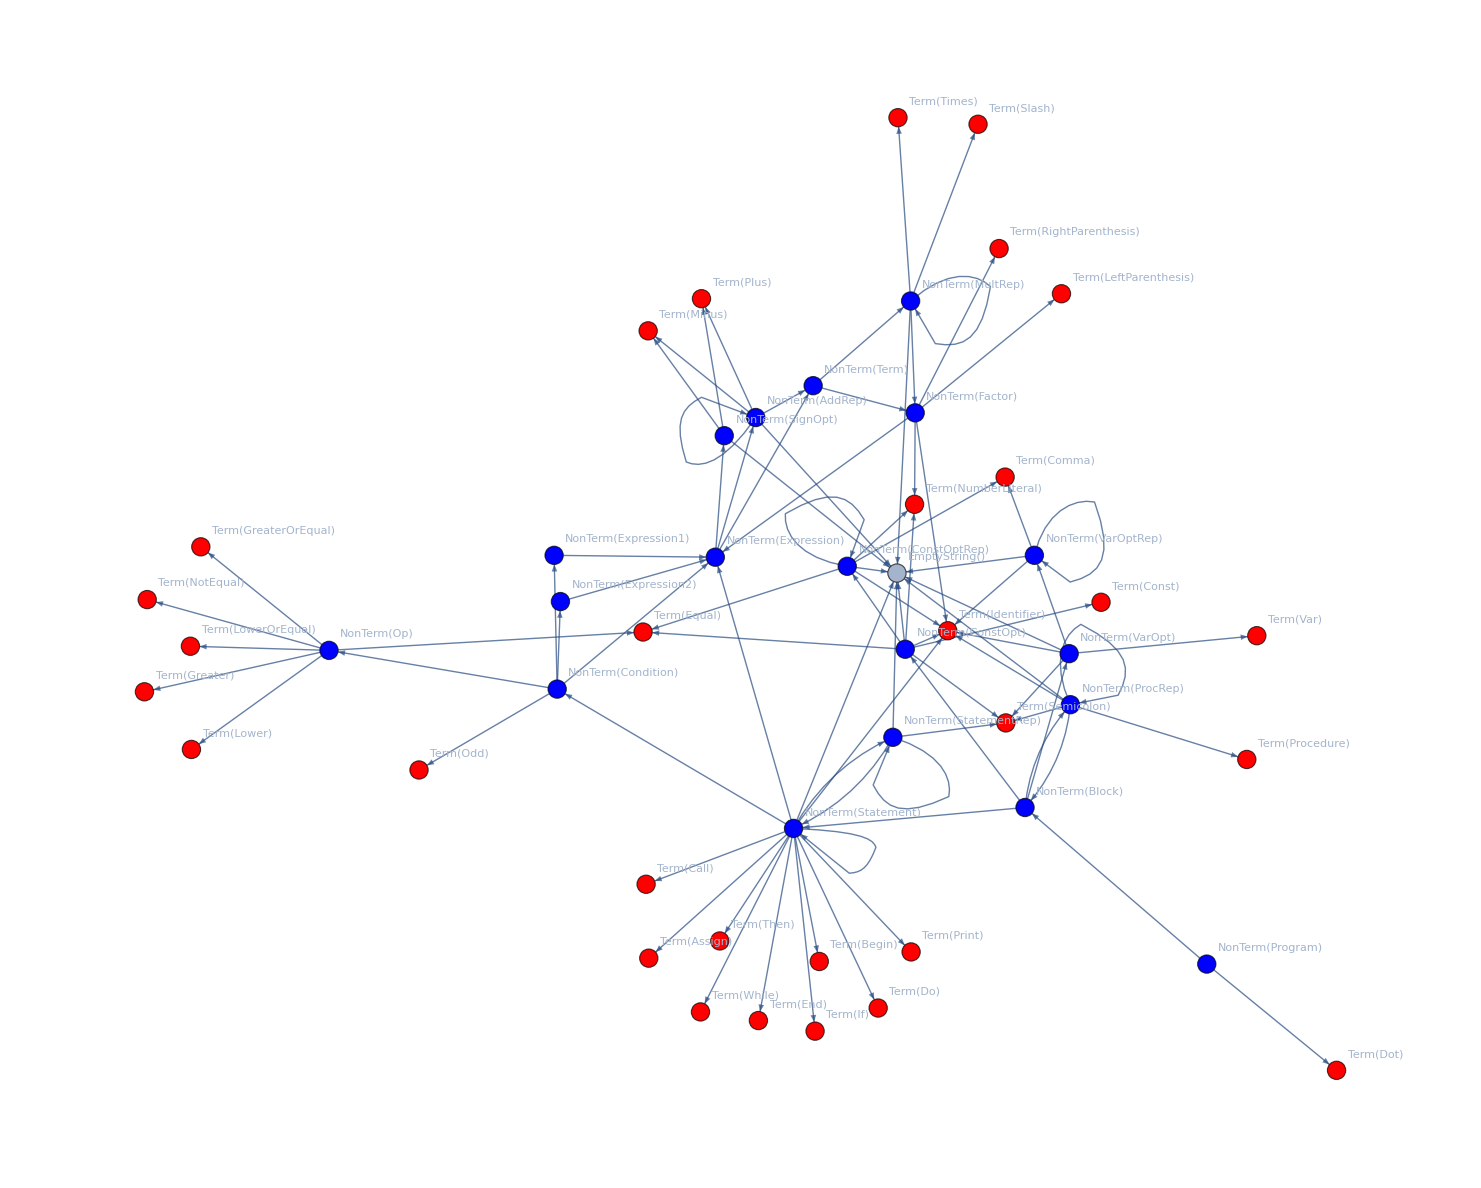

```mathematica
GrammarGraph[grammar]
```

```mathematica
testProgram =
"procedure primes;
var arg;
begin
    arg := 2;
    while odd arg do
    begin
       arg := arg + 1
    end
end;

call primes.";
```

```mathematica
tokens = Tokenize[testProgram,symbolRecognizer,keywordRecognizer];
```

```mathematica
tokens
```

{<|Type→Procedure,Value→procedure|>,<|Type→Identifier,Value→primes|>,<|Type→Semicolon,Value→;|>,<|Type→Var,Value→var|>,<|Type→Identifier,Value→arg|>,<|Type→Semicolon,Value→;|>,<|Type→Begin,Value→begin|>,<|Type→Identifier,Value→arg|>,<|Type→Assign,Value→:=|>,<|Type→NumberLiteral,Value→2|>,<|Type→Semicolon,Value→;|>,<|Type→While,Value→while|>,<|Type→Odd,Value→odd|>,<|Type→Identifier,Value→arg|>,<|Type→Do,Value→do|>,<|Type→Begin,Value→begin|>,<|Type→Identifier,Value→arg|>,<|Type→Assign,Value→:=|>,<|Type→Identifier,Value→arg|>,<|Type→Plus,Value→+|>,<|Type→NumberLiteral,Value→1|>,<|Type→End,Value→end|>,<|Type→End,Value→end|>,<|Type→Semicolon,Value→;|>,<|Type→Call,Value→call|>,<|Type→Identifier,Value→primes|>,<|Type→Dot,Value→.|>}

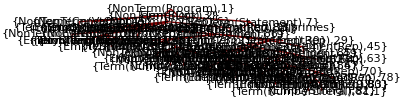

```mathematica
ParseTree[tokens,grammar]
```

```mathematica
Dataset@Parse[tokens,grammar,"Trace"->True]
```

Dataset[<>]

```mathematica
parseTree = Parse[tokens,grammar] ;
```

Parse tree synthesization

After the construction of the parse tree, the intermediate code can be constructed by using associated semantic rules that are evaluated from children nodes to parents.

GetAction[treeSymbol, parseTree] returns the semantic action corresponding to the parseTree. 
SynthesizeNonTerm[treeSymbol, parseTree, synthesizations] creates the synthesization for the nonterminal treeSymbol.
SynthesizeTerm[treeSymbol, synthesizations] creates the synthesization for the terminal treeSymbol.
SynthesizeTree[parseTree] synthesizes the parseTree by using the semantic actions in the grammar.

In the following grammar, for the second production rule, the grammar entry with associated action would be represented by
{
    “From” -> NonTerm[“E”], 
    “To”-> {NonTerm[“E”], Term[“+“], NonTerm[“T”]}},
    “Action”->{“val”->NonTerm[“E”][“val”] + NonTerm[“T”][“val”]}
 }.

In general, for any given grammar production rule, it will be represented as
<|”From”-> label, "To"->{X_1,... , X_n}, "Action"->{l_1:> f_1,... , l_m:> f_m} |>
where label is the name of a NonTerminal,  each X_i is a Terminal or NonTerminal, l_iis a property of the NonTerm[label] and f_i are functions that are evaluated with values synthesized from X_1,... , X_n.

```mathematica
GetAction[treeSymbol_,parseTree_]:=Block[{children,replaceTerms,action},
(* 
   Get the grammar action formatted for a given symbol. For example, for a parse tree where the symbol
  {NonTerm["Statement"],19} has the associated action
  {"Value":>"","TACode":>ColumnJoin[{NonTerm["Statement"]["TACode"],NonTerm["StatementRep"]["TACode"]}]},
   executing
  GetAction[{NonTerm["Statement"],19},parseTree] will return
  {"Value":>"","TACode":>ColumnJoin[{{NonTerm["Statement"],28}["TACode"],{NonTerm["StatementRep"],29}["TACode"]}]}
*)
children = Cases[First[parseTree],HoldPattern[treeSymbol->c_]:>c];
replaceTerms = Map[First[#]->Take[#,2]&,children];
action = Last[FirstCase[Last[parseTree],{treeSymbol,_}]];

ReplaceAll[action,replaceTerms]
];
```

```mathematica
SynthesizeNonTerm[treeSymbol_,parseTree_,synthesizations_]:=Block[{eval,new},
(* Synthesize from values obtained in past synthesizations *)
eval = ReplaceAll[GetAction[treeSymbol,parseTree],synthesizations];
If[eval === Missing["KeyAbsent","Action"], Return[synthesizations]];

new = Map[treeSymbol[First[#]]->Last[#]&,eval];
Return[Join[new,synthesizations]]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]>2,
Prepend[synthesizations, Take[treeSymbol,2]["Value"] ->Last[treeSymbol]],
synthesizations
]
];
```

```mathematica
SynthesizeTree[parseTree_]:=Block[{startSymbol,depthFirstScan,symbolType,synthesized},
ResetVarGenerator[];
ResetLabelGenerator[];

(* Walk the parse tree in post order *)
startSymbol = parseTree[[1,1,1]];
depthFirstScan = First[Last[Reap[
DepthFirstScan[Graph[First[parseTree]],startSymbol,{"PostvisitVertex"->(Sow[#]&)}]
]
]];

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[First[s]];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,parseTree,synthesized]];
,
{s,depthFirstScan}
];

Return[synthesized];
];
```

```mathematica
FormatSynthValues[groupedSynthetization_]:=MapAt[First[Level[#,2]]&,groupedSynthetization,{All,1}];
Synthesis[parseTree_]:=ReplaceAll[{NonTerm["Program"],1}["TACode"],SynthesizeTree[parseTree]];
ViewSynthesisProcess[parseTree_]:=Block[{grouped},
grouped = GroupBy[SynthesizeTree[parseTree],Head[First[#]]&];
Dataset@Map[FormatSynthValues,grouped]
];
```

#### Examples

```mathematica
testProgram =
"var n;
begin
   n := 0;
   if n # 10 then
   begin
      print n;
      n := n + 1;
   end;
end.";
tokens = Tokenize[testProgram,symbolRecognizer,keywordRecognizer];
parseTree = Parse[tokens,grammar] ;
Synthesis[parseTree]
ViewSynthesisProcess[parseTree]
```

set <n> 0
compare <n> 10
if_not_equal <0::L>
print <n>
add $0 <n> 1
set <n> $0
label <0::L>
return
declare_var <n>

Dataset[<>]

Compilation to intermediate code

Since the tree synthesization is L-Attributed, meaning that every node can only synthesize from its children, variables inside procedures “cannot see” if there is already another variable in the global space with the same name. This is not a problem since we can label variables inside procedures to differenciate them from their global counterparts. This is done by ProcedureProcessTags for each procedure. ICProcessTags does this but for the whole synthesized tree. The resulting code is a form of intermediate code that can be translated to any target machine.

ProcedureProcessLabels[ic, from, to, globalVar] processes the procedure enclosed in [from, to] changing the labels to reflect that symbols in the interval belong to the corresponding procedure. Labels in globalVars are left unprocessed.
ICProcessLabels[ic] processes all the labels in ic.
PL0ParseAndSynthesize[code] returns ic without processing the labels.
PL0CompileToIC[code] returns ic with processed labels.
PlotIC[ic] graphical representation of IC.

```mathematica
IsLabelQ[s_]:=And[StringStartsQ[s, "<"], StringEndsQ[s, ">"]];
IsTempQ[s_]:=StringStartsQ[s, "$"];
InsertSequence[l1_,l2_,n_]:=FlattenAt[Insert[l1,l2,n],n];

ProcedureProcessLabelsAndTemps[ic_,from_,to_,globalVar_]:=Block[{name,procInstructions,labels,tempSymbols,replaceLabelsRules,replaceTempSymbolsRules,tempDeclarations,processed},
name = StringReplace[Last[Extract[ic,{from}]],"<"~~x__~~">":>x];
procInstructions = Flatten[Take[ic,{from+1,to-1}]];
labels = DeleteDuplicates[Select[procInstructions,IsLabelQ[#]&&!MemberQ[globalVar,#]&]];
tempSymbols = DeleteDuplicates[Select[procInstructions,IsTempQ]];
replaceLabelsRules = Map[#->StringReplace[#,"<"~~x__~~">":>StringJoin["<",name,"::",x,">"]]&,labels];
replaceTempSymbolsRules = Map[#->StringJoin["<",name,"::",#,">"]&,tempSymbols];
tempDeclarations = Thread[{"declare_var",replaceTempSymbolsRules[[All,2]]}];

processed = ReplaceAll[Take[ic,{from,to}],  Join[replaceLabelsRules,replaceTempSymbolsRules]];
processed = InsertSequence[processed,tempDeclarations,-2];
Return[processed];
];
GlobalProcessLabelsAndTemps[ic_]:=Block[{procInstructions,tempSymbols,replaceTempSymbolsRules,tempDeclarations,processed},
procInstructions = Flatten[ic];
tempSymbols = DeleteDuplicates[Select[procInstructions,IsTempQ]];
replaceTempSymbolsRules = Map[#->StringJoin["<",#,">"]&,tempSymbols];
tempDeclarations = Thread[{"declare_var",replaceTempSymbolsRules[[All,2]]}];
processed = ReplaceAll[ic,  replaceTempSymbolsRules];
processed = InsertSequence[processed,tempDeclarations,-2];
Return[processed];
];
ICProcessLabelsAndTemps[ic_]:=Block[{splitted,preProc,pos,parts,processed,postProc,globalVar,allProcessed,procICCode},
splitted = Map[StringSplit,StringSplit[ic,"\n"]];
pos = Flatten[Position[splitted,{"begin_proc",_}|{"end_proc",_}]];
If[pos ≠ {},
preProc = GlobalProcessLabelsAndTemps[Take[splitted,{1,First[pos]-1}]];
postProc = GlobalProcessLabelsAndTemps[Take[splitted,{Last[pos]+1,Length[splitted]}]];
globalVar = Cases[Join[preProc,postProc],{"declare_var",label_}:>label];

parts = Partition[pos,2];
processed = Map[ProcedureProcessLabelsAndTemps[splitted,First[#],Last[#],globalVar]&,parts];

allProcessed = Join[preProc,Concatenate[processed],postProc];
,
allProcessed = GlobalProcessLabelsAndTemps[splitted];
];
procICCode = StringJoin[Riffle[Map[LineJoin,allProcessed],"\n"]];
Return[procICCode];
];
```

```mathematica
PL0ParseAndSynthesize[code_]:=Block[{tokens,parseTree,synthesized},
(* Return tree synthesis without label processing (may present namespace conflicts) *)
tokens = Tokenize[code,symbolRecognizer,keywordRecognizer];
parseTree = Parse[tokens,grammar] ;
synthesized = ReplaceAll[{NonTerm["Program"],1}["TACode"],SynthesizeTree[parseTree]];
Return[synthesized];
];
PL0CompileToIC[code_]:=ICProcessLabelsAndTemps[PL0ParseAndSynthesize[code]];
```

```mathematica
PlotIC[ic_]:=Block[{splitted,completed},
splitted = Map[StringSplit,StringSplit[ic,"\n"]];
completed = Map[PadRight[#,4,""]&,splitted];

Grid[
Prepend[completed,{"Instruction","P1","P2","P3"}],
Background->{{LightGreen},{LightRed}},
Frame->True
]
];
```

### Example

```mathematica
program = "var n;
begin
   n := 0;
   if n # 10 then
   begin
      print n;
      n := n + 1;
   end;
end.";
```

```mathematica
PL0CompileToIC[program]
```

set <n> 0
compare <n> 10
if_not_equal <0::L>
print <n>
add $0 <n> 1
set <n> $0
label <0::L>
return
declare_var <n>

```mathematica
PlotIC@PL0CompileToIC[program]
```

Instruction | P1 | P2 | P3
set | <n> | 0 | 
compare | <n> | 10 | 
if_not_equal | <0::L> |  | 
print | <n> |  | 
add | $0 | <n> | 1
set | <n> | $0 | 
label | <0::L> |  | 
return |  |  | 
declare_var | <n> |  |

## Assembly code generation

Intermediate code is converted directly to assembler by simple substitution rules. Also, some standard routines like multiplication or division have to be appended at the end of the ASM code.

CompileICToASM[ic] compiles intermediate code into assembler.
CompilePL0ToASM[code] compiles PL/0 code into assembler.

Common routines

Since the target machine doesn’t have native instructions for implementing multiplication or division, we can add them as procedures.

```mathematica
divisionRoutine = "Label <divide>
LoadA <divide::zero>
Store <divide::result>
Label <divide::begin_loop>
LoadA <divide::result>
Increment
Store <divide::result>
LoadA <divide::n1>
LoadB <divide::n2>
Substract
Store <divide::n1>
JumpNeg <divide::end_loop>
Jump <divide::begin_loop>
Label <divide::end_loop>
LoadA <divide::result>
Decrement
Return
Declare <divide::n1> 0
Declare <divide::n2> 0
Declare <divide::result> 0
Declare <divide::zero> 0";
multiplicationRoutine = "Label <multiply>
LoadA <multiply::zero>
Store <multiply::result>
Label <multiply::begin_loop>
LoadA <multiply::result>
LoadB <multiply::n2>
Add
Store <multiply::result>
LoadA <multiply::n1>
Decrement
Store <multiply::n1>
JumpZero <multiply::end_loop>
Jump <multiply::begin_loop>
Label <multiply::end_loop>
Return
Declare <multiply::n1> 0
Declare <multiply::n2> 0
Declare <multiply::result> 0
Declare <multiply::zero> 0";
```

Intermediate code to assembly conversion rules

```mathematica
(* Intermediate code can be mapped directly to assembler with a substitution rule *)
icToAsmRules = {
{"call",label_}:>{{"Call", label}},
{"print",label_}:>{{"Print", label}},
{"return"}->{{"Return"}},
{"begin_proc",label_}:>{{"Label",label}},{"end_proc",_}:>Nothing,
{"label",label_}:>{{"Label", label}},
{"goto",label_}:>{{"Jump",label}},
{"declare_var",label_}:>{{"Declare",label,"0"}},
{"declare_const",label_,n_}:>{{"Declare",label,n}},

{"set",out_/;IsLabelQ[out],n_/;!IsLabelQ[n]}:> {{"SetA",n},{"Store",out}},
{"set",out_/;IsLabelQ[out],l_/;IsLabelQ[l]}:> {{"LoadA",l},{"Store",out}},

{"compare",l1_/;IsLabelQ[l1],l2_/;IsLabelQ[l2]}:>{{"LoadA",l1},{"LoadB",l2},{"Substract"}},
{"compare",l_/;IsLabelQ[l],n_/;!IsLabelQ[n]}:>{{"LoadA",l},{"SetB",n},{"Substract"}},
{"compare",n_/;!IsLabelQ[n],l_/;IsLabelQ[l]}:>{{"SetA",n},{"LoadB",l},{"Substract"}},

{"if_less",label_}:>{{"JumpNeg",label}},
{"if_greater",label_}:>{{"JumpPos",label}},
{"if_equal",label_}:>{{"JumpNotZero",label}},
{"if_not_equal",label_}:>{{"JumpZero",label}},
{"if_less_or_equal",label_}:>{{"JumpNeg",label},{"JumpNotZero",label}},
{"if_greater_or_equal",label_}:>{{"JumpPos",label},{"JumpNotZero",label}},
{"if_odd",label_}:>{{"JumpOdd",label}},

{"odd",l_/;IsLabelQ[l]}:>{{"LoadA",l}},
{"odd",n_/;!IsLabelQ[n]}:>{{"SetA",n}},

{"add",out_,l1_/;IsLabelQ[l1],l2_/;IsLabelQ[l2]}:>{{"LoadA",l1},{"LoadB",l2},{"Add"},{"Store",out}},
{"add",out_,n1_/;!IsLabelQ[n1],n2_/;!IsLabelQ[n2]}:>{{"SetA",n1},{"SetB",n2},{"Add"},{"Store",out}},
{"add",out_,l_/;IsLabelQ[l],n_/;!IsLabelQ[n]}:>{{"LoadA",l},{"SetB",n},{"Add"},{"Store",out}},
{"add",out_,n_/;!IsLabelQ[n],l_/;IsLabelQ[l]}:>{{"SetA",n},{"LoadB",l},{"Add"},{"Store",out}},

{"substract",out_,l1_/;IsLabelQ[l1],l2_/;IsLabelQ[l2]}:>{{"LoadA",l1},{"LoadB",l2},{"Substract"},{"Store",out}},
{"substract",out_,n1_/;!IsLabelQ[n1],n2_/;!IsLabelQ[n2]}:>{{"SetA",n1},{"SetB",n2},{"Substract"},{"Store",out}},
{"substract",out_,l_/;IsLabelQ[l],n_/;!IsLabelQ[n]}:>{{"LoadA",l},{"SetB",n},{"Substract"},{"Store",out}},
{"substract",out_,n_/;!IsLabelQ[n],l_/;IsLabelQ[l]}:>{{"SetA",n},{"LoadB",l},{"Substract"},{"Store",out}},

{"multiply",out_,l1_/;IsLabelQ[l1],l2_/;IsLabelQ[l2]}:>{{"LoadA",l1},{"Store","<multiply::n1>"},{"LoadA",l2},{"Store","<multiply::n2>"},{"Call","<multiply>"},{"Store",out}},
{"multiply",out_,n1_/;!IsLabelQ[n1],n2_/;!IsLabelQ[n2]}:>{{"SetA",n1},{"Store","<multiply::n1>"},{"SetA",n2},{"Store","<multiply::n2>"},{"Call","<multiply>"},{"Store",out}},
{"multiply",out_,l_/;IsLabelQ[l],n_/;!IsLabelQ[n]}:>{{"LoadA",l},{"Store","<multiply::n1>"},{"SetA",n},{"Store","<multiply::n2>"},{"Call","<multiply>"},{"Store",out}},
{"multiply",out_,n_/;!IsLabelQ[n],l_/;IsLabelQ[l]}:>{{"SetA",n},{"Store","<multiply::n1>"},{"LoadA",l},{"Store","<multiply::n2>"},{"Call","<multiply>"},{"Store",out}},

{"divide",out_,l1_/;IsLabelQ[l1],l2_/;IsLabelQ[l2]}:>{{"LoadA",l1},{"Store","<divide::n1>"},{"LoadA",l2},{"Store","<divide::n2>"},{"Call","<divide>"},{"Store",out}},
{"divide",out_,n1_/;!IsLabelQ[n1],n2_/;!IsLabelQ[n2]}:>{{"SetA",n1},{"Store","<divide::n1>"},{"SetA",n2},{"Store","<divide::n2>"},{"Call","<divide>"},{"Store",out}},
{"divide",out_,l_/;IsLabelQ[l],n_/;!IsLabelQ[n]}:>{{"LoadA",l},{"Store","<divide::n1>"},{"SetA",n},{"Store","<divide::n2>"},{"Call","<divide>"},{"Store",out}},
{"divide",out_,n_/;!IsLabelQ[n],l_/;IsLabelQ[l]}:>{{"SetA",n},{"Store","<divide::n1>"},{"LoadA",l},{"Store","<divide::n2>"},{"Call","<divide>"},{"Store",out}}
};
CompileICToASM[ic_]:=Block[{splitted,replaced,generatedCode},
splitted = Map[StringSplit,StringSplit[ic,"\n"]];
replaced = ReplaceAll[splitted,icToAsmRules];
generatedCode = ColumnJoin[Map[LineJoin,Concatenate[replaced]]];
If[StringContainsQ[generatedCode,"multiply"],
generatedCode = ColumnJoin[{generatedCode,multiplicationRoutine}]
];
If[StringContainsQ[generatedCode,"divide"],
generatedCode = ColumnJoin[{generatedCode,divisionRoutine}]
];
Return[generatedCode];
];

CompilePL0ToASM[code_]:=CompileICToASM[PL0CompileToIC[code]];
```

### Example

```mathematica
CompilePL0ToASM["
var n;
procedure count;
begin
   n := 0;
   while n # 10 do
   begin
      n := n + 1;
   end
end

begin
    call count;
    print n
end."]
```

Call <count>
Print <n>
Return
Label <count>
SetA 0
Store <n>
Label <count::0::L1>
LoadA <n>
SetB 10
Substract
JumpZero <count::0::L2>
LoadA <n>
SetB 1
Add
Store <count::$0>
LoadA <count::$0>
Store <n>
Jump <count::0::L1>
Label <count::0::L2>
Return
Declare <count::$0> 0
Declare <n> 0

Machine code generation

For the conversion of ASM code to machine code all the labels (IC arguments enclosed in <>) need to be converted to memory positions. 
OpCode[mnemonic] returns the opcode associated with mnemonic.
GetInstructions[asmcode] formats assembly code into a nested list.
GetPosition[instructions, token] calculates the final position of a given token considering that Labels occupy 0 bits in the machine code, Declare 1 byte, and any other instruction 2 bytes.
ProcessTags[instructions] generates the substitution rule for converting labels to memory positions.
MachineInstructions[instructions] returns the exact instructions that will be assembled.
AssemblyCompile[asmcode] compiles ASM to machine code.
InstructionsPlot[asmcode] returns a visualization of the program in a graphical panel.
PL0Compile[code] compiles PL/0 code to machine code.

```mathematica
cpuMnemonics = {
"LoadA","LoadB","SetA","SetB","Store","Add",
"Substract","Increment","Decrement","Jump","JumpPos","JumpNeg","JumpZero","JumpNotZero","JumpOdd",
"Call","Return","Print","Halt"
};
opcodes = Thread[cpuMnemonics->Take[Tuples[{0,1},8],Length[cpuMnemonics]]];
revOpcodes = Map[Reverse,opcodes];
OpCode[mnemonic_]:=ReplaceAll[mnemonic,opcodes];
```

```mathematica
DecimalToBinary[n_,size_ :8]:=PadLeft[IntegerDigits[n,2],size];
BinaryToDecimal[l_]:=FromDigits[l,2];
GetInstructions[asmcode_]:=Block[{separated,completed},
separated = DeleteCases[Map[StringSplit,StringSplit[asmcode,"\n"]],{}];
completed = ReplaceAll[separated,l_/;(Length[l]==1):>Append[l,0]];
Return[completed];
];
GetPosition[instructions_,token_]:=Block[{pos,labels,countingRules},
pos = Position[instructions,token];
If[Length[pos]>1,Return[$Failed]];
labels = Take[instructions,pos[[1,1]]-1][[All,1]];
countingRules = Join[Thread[cpuMnemonics->2],{"Label"->0,"Declare"->1}];

Total[ReplaceAll[labels,countingRules]]
];
ProcessTags[instructions_]:=Block[{labels,variablePos},
labels = Cases[instructions,{"Label",tag_}:>(tag->GetPosition[instructions,{"Label",tag}])];
variablePos = Cases[instructions,{"Declare",tag_,value_}:>(tag->GetPosition[instructions,{"Declare",tag,value}])];
Join[labels,variablePos]
];
MachineInstructions[instructions_]:=Block[{setNumeric,removeLabels,replaceTags},
setNumeric = ReplaceAll[instructions,{{"Declare",_,value_}:>ToExpression[value],{"SetA",value_}:>{"SetA",ToExpression[value]},{"SetB",value_}:>{"SetB",ToExpression[value]} }];
removeLabels = DeleteCases[setNumeric,{"Label",__}];
replaceTags = ReplaceAll[removeLabels,ProcessTags[instructions]];

Return[replaceTags];
];
AssemblyCompile[asmcode_]:=Block[{linearized,rules, machineCode},
linearized = Flatten[MachineInstructions[GetInstructions[asmcode]]];
rules = Append[opcodes,n_Integer:>DecimalToBinary[n]];
machineCode = ReplaceAll[linearized,rules];
Return[machineCode];
];
InstructionsPanel[machineInstructions_,from_]:=Block[{cursor,instructions},
If[Negative[cursor], cursor = 0];
instructions = Thread[{Range[from,from+Length[Flatten[machineInstructions]]-1],Flatten[machineInstructions]}];

Grid[
instructions,
Background->{{LightGreen},{}}
]
];
InstructionsPlot[asmcode_]:=Block[{mi,tabs,currentAddress},
mi =Flatten[ MachineInstructions[GetInstructions[asmcode]]];
tabs = MapThread[InstructionsPanel,{Partition[mi,UpTo[16]],Range[0,Length[mi],16]}];

Panel[TabView[Thread[Range[0,Length[mi],16]->tabs]],Style["Program",Bold]]
];
PL0Compile[code_]:=AssemblyCompile[CompilePL0ToASM[code]];
```

### Example

```mathematica
program = "var n;
procedure count;
begin
   n := 0;
   while n # 10 do
   begin
      n := n + 1;
   end
end

begin
    call count;
    print n
end.";
Lint[program,symbolRecognizer,keywordRecognizer,colorRules]
```

var n;
procedure count;
begin
   n := 0;
   while n # 10 do
   begin
      n := n + 1;
   end
end

begin
    call count;
    print n
end.

```mathematica
asm = CompilePL0ToASM[program];
```

```mathematica
MachineInstructions[GetInstructions[asm]]
```

{{Call,6},{Print,35},{Return,0},{SetA,0},{Store,35},{LoadA,35},{SetB,10},{Substract,0},{JumpZero,32},{LoadA,35},{SetB,1},{Add,0},{Store,34},{LoadA,34},{Store,35},{Jump,10},{Return,0},0,0}

```mathematica
PL0Compile[program]
```

{{0,0,0,0,1,1,1,1},{0,0,0,0,0,1,1,0},{0,0,0,1,0,0,0,1},{0,0,1,0,0,0,1,1},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,1},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,1},{0,0,0,0,0,0,1,1},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,1},{0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,1},{0,0,0,0,1,0,0,1},{0,0,0,0,1,0,1,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}